```mathematica
Mz=91.2;
mt=173;
yu=√2*.00216/246.22;
yd=√2*.0047/246.22;
ys=√2*.0935/246.22;
yc=√2*1.273/246.22;
yb=√2*4.183/246.22;
yt=√2*172.57/246.22;
```

#### QCD RG

```mathematica
b0QCD[Nf_,Ns_]:=11-(Ns/6)-(2*Nf/3)
```

```mathematica
alphaQCDb[Λ_,b_,fa_]:=If[Λ<mt,2*Pi*((2*Pi)/0.12-(23/3)*Log[Mz/Λ])^-1,If[Λ<fa,2*Pi*((2*Pi)/0.12-(23/3)*Log[Mz/mt]-7*Log[mt/Λ])^-1,2*Pi*((2*Pi)/0.12-(23/3)*Log[Mz/mt]-7*Log[mt/fa]-b*Log[fa/Λ])^-1]]
```

#### Instanton pre-factors

```mathematica
constInstanton[Nf_,Ns_]:= (1.5*10^-3)*Exp[(Nf-Ns/2).292]
```

```mathematica
YukK=((40/9)*yu*yd*ys*yc*yt*yb)/(4*Pi)^6;
```

## Product Group Models

#### (SU(3))^N→ SU(3) for a two KSVZ fermions

for i=1, we have

```mathematica
b12=b0QCD[6+2,3];
```

```mathematica
C12=constInstanton[6+2,3] /(24*Pi^2)/4;
```

for i=2,...,N-1,  we have

```mathematica
b22=b0QCD[02,6];
```

```mathematica
C22=constInstanton[02,6]/(24*Pi^2)/4;
```

```mathematica
(*C2a=constInstanton[0,6] *)
```

for i=N, we have

```mathematica
bN2=b0QCD[ 02,3];
```

```mathematica
(*bNa=b0QCD[ 0,3]*)
```

```mathematica
CN2=constInstanton[ 02,3] /(24*Pi^2)/4;
```

computing the ρ integral with two KSVZ fermions

for i=1,N

```mathematica
Integrate[r^(b-5)*Exp[-4*Pi^2*r^2*v^2],{r,0,Infinity}]//FullSimplify
```

ConditionalExpression[2^(3-b) π^(4-b) v^4 (v^2)^(-b/2) Gamma[-2+b/2], Re[b]>4&&((Re[v^2]==0&&Re[b]<5)||Re[v^2]>0)]

for i=2,...N-1, v --> √2 v

Note that qcd runnings contribution from all KSVZ fermions

```mathematica
bQCD2=b0QCD[6+2,0];
```

for α_2=α_3

```mathematica
QCDAxionMass[fa_]:=5.70*10^(-6-9+12)/fa;
```

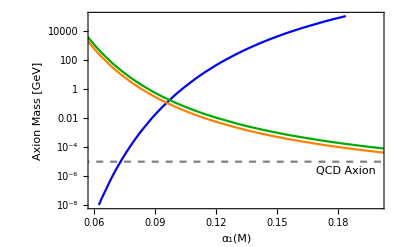

```mathematica
alpha2[Λ_,bQCD_,fa_, alpha1_]:=2/(1/alphaQCDb[Λ,bQCD,fa]-1/alpha1);
AxionMass12[fa_,v_,alpha1_]:=1/fa* Sqrt[2*C12*YukK*1/2*(2*Pi)^(4-b12)*Gamma[1/2 (-4+b12)]*v^4*((2*Pi)/alpha1)^6*Exp[-(2*Pi)/alpha1]];
AxionMass22[fa_,v_,alpha1_]:=1/v* Sqrt[2*C22*1/2*2^(4/2-b22/2)*(2*Pi)^(4-b22) *Gamma[1/2 (-4+b22)]*v^4*((2*Pi)/alpha2[v,bQCD2,fa, alpha1])^6*Exp[-(2*Pi)/alpha2[v,bQCD2,fa, alpha1]]];
AxionMass32[fa_,v_,alpha1_]:=1/v* Sqrt[2*CN2*1/2*(2*Pi)^(4-bN2) *Gamma[1/2 (-4+bN2)]*v^4*((2*Pi)/alpha2[v,bQCD2,fa, alpha1])^6*Exp[-(2*Pi)/alpha2[v,bQCD2,fa, alpha1]]]; 
Plotα23fv=Show[LogPlot[{AxionMass12[500,20*10^11,x],AxionMass22[500,20*10^11,x],AxionMass32[500,20*10^11,x]} ,{x,.01,4},PlotStyle->{Blue,Orange, Darker[ Green]}  ,PlotRange->{{.06,.2},{10^-8,10^5}},Frame-> True, FrameLabel->{ "α_1(M)","Axion  Mass [GeV]"} ],LogPlot[ QCDAxionMass[600] ,{x,.01,2},PlotStyle->{Dashed,Gray}  ,PlotRange->{{.06,.4},{10^-8,10^9}}, PlotLegends->{Placed["QCD Axion",{0.87,0.19}],Placed[SwatchLegend[{Blue,Orange, Darker[ Green]} ,{-Graphics-,-Graphics-,-Graphics-},LegendMarkerSize->10,(*LegendLayout ->"Row",*)LegendMarkers->"Bubble",LabelStyle->{FontSize->3}],{0.9,.7}] }]]
```

```mathematica
Solve[D[AxionMass12[fa,v,a],a]==0,a]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→1.0472}}

```mathematica
Solve[D[a^-6 Exp[-2*Pi/a],a]==0,a]
```

{{a→π/3}}

```mathematica
AxionMass1[f_,v_]:=AxionMass12[f,v,1.0472]//PowerExpand
```

```mathematica
MaxAxionMassProdGroup9=Interpolation[Table[{ AxionMass1[10^f,10^9]  ,10^f},{f,-10,10,.1}] ];
```

```mathematica
MaxAxionMassProdGroup11=Interpolation[Table[{ AxionMass1[10^f,10^11]  ,10^f},{f,-10,10,.1}] ]; 
MaxAxionMassProdGroup13=Interpolation[Table[{ AxionMass1[10^f,10^13]  ,10^f},{f,-10,10,.1}] ];
```

```mathematica
<<MaTeX`
```

```mathematica
MaTeX[Product, FontSize->18]
```

-Graphics-

```mathematica
MaTeX[Group, FontSize->18]
```

-Graphics-

```mathematica
MaTeX[Model, FontSize->18]
```

-Graphics-

```mathematica
MaTeX[M  "=10^11", FontSize->14]
```

-Graphics-

```mathematica
ticksSublist=Flatten[Table[{{i*10.^j,"",{.005,0}}},{i,2,9,1},{j,-8,-1,1}],2];
ticksSublist2=Flatten[Table[{{i*10.^j,"",{.005,0}}},{i,2,9,1},{j,-8,8,1}],2];
```

```mathematica
ticksList={{Join[{ {10^-1,"10",{.01,0}},{10^-2,"10^2",{.01,0}},{10^-3,"10^3",{.01,0}},{10^-4,"10^4",{.01,0}}, {10^-5,"10^5",{.01,0}}, {10^-6,"10^6",{.01,0}}, {10^-7,"10^7",{.01,0}}, {10^-8,"10^8",{.01,0}}},ticksSublist],Automatic},{Join[{ {10^-3,"10^-3",{.01,0}}, {10^-2,"10^-2",{.01,0}},{10^-1,"10^-1",{.01,0}},{10^0,"1",{.01,0}},{10^1,"10",{.01,0}},{10^2,"10^2",{.01,0}},{10^3,"10^3",{.01,0}},{10^4,"10^4",{.01,0}}, {10^5,"10^5",{.01,0}}, {10^6,"10^6",{.01,0}}, {10^7,"10^7",{.01,0}}},ticksSublist2],Automatic}};
```

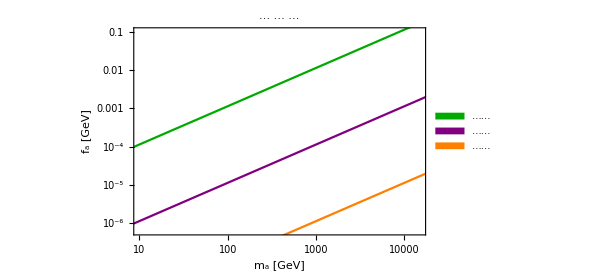

```mathematica
qcdAxion=LogLogPlot[ x/0.005625 ,{x,10^-14,10^10},PlotStyle->Black  ,PlotRange->{{10^1,1.5*10^4},{10^-6.2,.10 }},Frame-> True, FrameTicks->ticksList,FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]},
 
PlotLegends->   { Placed[SwatchLegend[{Darker[Green],Purple,Orange },{"(*GraphicsBox[{Thickness[0.018494544109487702`], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11XlIVEEYAPA1TdjIdNdrj2di67bqus9MMyuzrzsrUzRqIyEr16Msk4rI
WsgzSkszzaNNTQmJFCXQ0tBOibIytf7xjxQUytDIDovyaGee73vE4sDj8YN5
M/N98808jwMpUQZrkUhkZX7izM8c85NlF9FQZGCBvjtm3mbXq4cyK+z8wClv
62ebQMEjx5uc/97RoQMDzC3aBz2gd73XXeWNLqPNGwzx5mbrByUF9mlB27zB
mYxbxMLmuo5aUfBC+NE+1pQwzoDmm+dwuVgBz1vvX7I9xkKd1HdBwgc5jpev
z42weit4r1rPvImRCfNv3Le2PFWCfpzbnhF40AF9q6920P+pvYVp3Nks+vnT
dfVJoSx+z/s6CWeFBC0ircrJwn4+tx3f2gj29XD/kdysm9UfD2nHS4w6iKfN
CSL7lGf3S3WQ5Wqcm5QzDy6RuBvduPcSMTwi67JWwuoTa42dJlsuby/kXP9N
U2saSN4q5DC0Yzh2snIS3aBs1r0c+bPmMhmnQDDNo0mGnqbNFZKLY1ODv0+g
nTOYoiW9k+iIobCeZY5ibh8YGXwyDh7uSl6A1pP3hD26n+zPmAPw39PyaJGg
uX5S9EjOkdylDyxN1+8g/9/meM70/+4L0EqBj5eUZ8B3CZr2VzrAK9Lq5PCM
5LFmPuwc7R0rtVKgnU4Xnnhtw6BpnV8VHEn632S4unWx4/Kf5Ab1ZJ5QF66/
I8vNs12we2tVu+GLAqLJ9+lyKCXxy5WQRtctgziy/YuVGO/96JX66VrBdF0b
GDQdP4+ZqXsZN08vMxO3DM/jOZuOfP/lLJiqVS0TtYLvskdrrExqLh4PhnOM
GrrIuL4KaCTnJFyN+aP7tUeFvhAS1hrfswi9viBTGn/R0nx98ebXT/erU3Bb
ytnRsp+Cd4tdzgekqNA0v1MqrCcaxylPtKz4nTjxiQbd9X7XiN8qL/Tk+MkB
U7cXjsffR7zDu6/ETGUKjiDnsMfSfP3x5uOl57ZQ8JaHRrdgjWC6P8c1Fs6j
4ynQdLrK2U3PkUQJQSFtUdfSNdx9kKnk7uudWi4Oax0kpnzNflGkhSySp186
cCX5qdbifUXvnRs6NL0H1ez/Nlia/1/8A1PArWE=
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJ+KB2j4PgxOcbWYYv5j0MpXaoOMP7fb6UP5giqOfQG
l6hMl0fwedxUS5le2cD5JsZAsNkEzu/xesVi0ojgy8yL0zztgIM/URXOTwgJ
Ul/AqerwIkv72/RaBB9mPowPsx/G36CXt5hRxhbOh7kfnY/uP+cJzUJpUQpw
/gPXeMdZDxXg/oXxYfbB+DD3wPgw/8L4MP+g81d+e1lxJgHBh5gjD/cvjA8z
H8aH2Q/jw/wL48Pcj86H+Q8AZ9azyg==
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4o16eYsZ7zg7/AcDcQcYf72QDl/6PEmHKd/Y
4mcsQfA/bwjInsWO4N/fxzfHmMnZQf2TystZnlJwfs39H7eMvWXgfFObvUHT
HurC+S28/uuntOrB+WdAoEfPIT0NCO45wfn2TY+Oz9js5PCmeKvo79O6DuJT
r3BmRDk5+F+cGPPvsA6Ev8gRg5+R/6H15BdtiP7TCD7YXBUnOH9N9+0MhnYn
BxbOLvnkdTpwPsz9MD7MfzNBoNEJNXyeOML5N6VrEo3WYvJh4Sv8yfF82l1H
h2jVCJlzMhIOb3j3GczscoLzwfJHEXweYDClMjjD+RURK0zPrkbw0eMPAIwj
zT8=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJJKP0rJvfov0nuDmdA4I2KA4z/Ikv723RbdYdlLzz0
/ne6O/wHgXpNh4v58eznPN0dZJYDJeZrO7ipljLNYnB3OL5rRy/bB10HBhBo
cIOY16MHkddA8ENKVKb/P+AK5z/YxzfH2MnV4SnIvr26DhbXjuaaMEDlc7Qd
9CYs+GF4zsVh+gT+KrPVmg4HamUt0ve4OBwD26cO58PcD+O/X7Re4ayFkkPd
b6uCcydcHMI5xdqN9RUcerxesZhwujrsCLaK+J8u41CyVfT3aT9Xh6r7P24Z
a0tA/HvS1aFNgV31zBUxiLyaG5wPdu8hBD+H8+eCdGl3hzdtud1GuyUdniQu
vGbi7+7wZd/HrenfZBx23ur6m9rv7mAMApMV4OEbAXKPv7IDeviDzeN2d/j1
9vUBS2dVOP+Opuya/8nKcP6e/Jq3M10VHb5sCMie9d3NQaRyUslZFXkHBceP
yWeuujkEvb38cQajpMNN6ZpEo1Q3hweu8Y6zPorD/QPj+5xgt5391hXOnwkC
la4Q936WcDihaTXpdLirw3ZQeLHLO2zUy1vM6OIKiWcDRTgf5h8YH+Z+GB8S
3+pw/pT21qjLczQh6SPB1UF86hXODCdthzXdtzMY6oHuiRDfflFBFxIfN10d
Thx2Wpv5Txfufhj/De8+g5lZCD44fi65OcwA+SNS16Ftefgpoy/A8AFF/Bct
ePhNBtkfownnN4DSiYY6RvgDAFiDZmQ=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQA2IQfQYERLwcUtOAgE3PAcZfcn8f35zFhg4siydZMbZ6
OthWRqww9TVykHf8mHxGFMEPLlGZ/v+CB5wPos5O9nAoWNN9O0PByCFSfPtF
hjgPh/8gsN7QQe1J87yzWh4O/SCN9oYOESB5Pg+HdJD91wzg/OkT+KvMpBH8
Fl7/9VOO6jps1MtbzFjj4XD+atgb/dvaEHPZPeH8tuXhp4xCEPydt7r+prZ7
OqxXBVq8VsehHSS/xNPhSeLCaybndeH8pyC+PoL/PEv72/S5Gg6gYDBW8nRo
YDnab7hd3eFifjz7uZsecP6Ub2zxM44g+ODwaPBwMLPZGzTtoDrE/niof7I1
HEDeTJuG4PMAvZW6wMNhcntr1OU/CP7fb6UP5gRqwvngeHmj6SA+9QpnRhPU
PnMth+Ktor9PpyH4IG+eDULwhT85nk/T9XDYYv7jUAoXgu+xv1bWwl0Tzt/h
0PTo+A91h7rfVgXnCjwcXoEM1lZ3+B2Te/TfLQQfHL41nnA+LL2YGAPBZU0H
9PQEAF3GDis=
"], CompressedData["
1:eJxTTMoPSmViYGAQA2IQfSE/nv3cQk8H/1vSNYmX9B1gfBNjENBzeJK48JpJ
uacDC2eXfLKfjkO31ysWE04EH6TN6KsHnF8ZscL07G4En3XxJCvGqR4OCSFB
6gs6dR3m2ehcmVXn4SA+9QpnhpMenL9BL28xo40+nM/rv35KqoQBnN8fXKIy
fT6Cr6+1UviCiKFD7W+rgnMzPBz+fit9MKfQ0OEN7z6Dmbs8HE4edlqb+c7Q
YdkLD73/Lz0cireK/j7NZ+Qg7/gx+YyoJ5wP9p8/gs8DsrfC04HbTbWUaZch
RH2vp8NMEPA0dDgDAnOg/J8G8PDaCHJ/DIIPC08A7eCRFQ==
"]}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3180342663856329],ImageSize->{54.06961892901619, 18.92083686176837},PlotRange->{{0., 54.07}, {0., 18.919999999999998`}}])","(*GraphicsBox[{Thickness[0.016963528413910096`], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11XlIVEEYAPA1TdjIdNdrj2di67bqus9MMyuzrzsrUzRqIyEr16Msk4rI
WsgzSkszzaNNTQmJFCXQ0tBOibIytf7xjxQUytDIDovyaGee73vE4sDj8YN5
M/N98808jwMpUQZrkUhkZX7izM8c85NlF9FQZGCBvjtm3mbXq4cyK+z8wClv
62ebQMEjx5uc/97RoQMDzC3aBz2gd73XXeWNLqPNGwzx5mbrByUF9mlB27zB
mYxbxMLmuo5aUfBC+NE+1pQwzoDmm+dwuVgBz1vvX7I9xkKd1HdBwgc5jpev
z42weit4r1rPvImRCfNv3Le2PFWCfpzbnhF40AF9q6920P+pvYVp3Nks+vnT
dfVJoSx+z/s6CWeFBC0ircrJwn4+tx3f2gj29XD/kdysm9UfD2nHS4w6iKfN
CSL7lGf3S3WQ5Wqcm5QzDy6RuBvduPcSMTwi67JWwuoTa42dJlsuby/kXP9N
U2saSN4q5DC0Yzh2snIS3aBs1r0c+bPmMhmnQDDNo0mGnqbNFZKLY1ODv0+g
nTOYoiW9k+iIobCeZY5ibh8YGXwyDh7uSl6A1pP3hD26n+zPmAPw39PyaJGg
uX5S9EjOkdylDyxN1+8g/9/meM70/+4L0EqBj5eUZ8B3CZr2VzrAK9Lq5PCM
5LFmPuwc7R0rtVKgnU4Xnnhtw6BpnV8VHEn632S4unWx4/Kf5Ab1ZJ5QF66/
I8vNs12we2tVu+GLAqLJ9+lyKCXxy5WQRtctgziy/YuVGO/96JX66VrBdF0b
GDQdP4+ZqXsZN08vMxO3DM/jOZuOfP/lLJiqVS0TtYLvskdrrExqLh4PhnOM
GrrIuL4KaCTnJFyN+aP7tUeFvhAS1hrfswi9viBTGn/R0nx98ebXT/erU3Bb
ytnRsp+Cd4tdzgekqNA0v1MqrCcaxylPtKz4nTjxiQbd9X7XiN8qL/Tk+MkB
U7cXjsffR7zDu6/ETGUKjiDnsMfSfP3x5uOl57ZQ8JaHRrdgjWC6P8c1Fs6j
4ynQdLrK2U3PkUQJQSFtUdfSNdx9kKnk7uudWi4Oax0kpnzNflGkhSySp186
cCX5qdbifUXvnRs6NL0H1ez/Nlia/1/8A1PArWE=
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJ+KB2j4PgxOcbWYYv5j0MpXaoOMP7fb6UP5giqOfQG
l6hMl0fwedxUS5le2cD5JsZAsNkEzu/xesVi0ojgy8yL0zztgIM/URXOTwgJ
Ul/AqerwIkv72/RaBB9mPowPsx/G36CXt5hRxhbOh7kfnY/uP+cJzUJpUQpw
/gPXeMdZDxXg/oXxYfbB+DD3wPgw/8L4MP+g81d+e1lxJgHBh5gjD/cvjA8z
H8aH2Q/jw/wL48Pcj86H+Q8AZ9azyg==
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4o16eYsZ7zg7/AcDcQcYf72QDl/6PEmHKd/Y
4mcsQfA/bwjInsWO4N/fxzfHmMnZQf2TystZnlJwfs39H7eMvWXgfFObvUHT
HurC+S28/uuntOrB+WdAoEfPIT0NCO45wfn2TY+Oz9js5PCmeKvo79O6DuJT
r3BmRDk5+F+cGPPvsA6Ev8gRg5+R/6H15BdtiP7TCD7YXBUnOH9N9+0MhnYn
BxbOLvnkdTpwPsz9MD7MfzNBoNEJNXyeOML5N6VrEo3WYvJh4Sv8yfF82l1H
h2jVCJlzMhIOb3j3GczscoLzwfJHEXweYDClMjjD+RURK0zPrkbw0eMPAIwj
zT8=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJJKP0rJvfov0nuDmdA4I2KA4z/Ikv723RbdYdlLzz0
/ne6O/wHgXpNh4v58eznPN0dZJYDJeZrO7ipljLNYnB3OL5rRy/bB10HBhBo
cIOY16MHkddA8ENKVKb/P+AK5z/YxzfH2MnV4SnIvr26DhbXjuaaMEDlc7Qd
9CYs+GF4zsVh+gT+KrPVmg4HamUt0ve4OBwD26cO58PcD+O/X7Re4ayFkkPd
b6uCcydcHMI5xdqN9RUcerxesZhwujrsCLaK+J8u41CyVfT3aT9Xh6r7P24Z
a0tA/HvS1aFNgV31zBUxiLyaG5wPdu8hBD+H8+eCdGl3hzdtud1GuyUdniQu
vGbi7+7wZd/HrenfZBx23ur6m9rv7mAMApMV4OEbAXKPv7IDeviDzeN2d/j1
9vUBS2dVOP+Opuya/8nKcP6e/Jq3M10VHb5sCMie9d3NQaRyUslZFXkHBceP
yWeuujkEvb38cQajpMNN6ZpEo1Q3hweu8Y6zPorD/QPj+5xgt5391hXOnwkC
la4Q936WcDihaTXpdLirw3ZQeLHLO2zUy1vM6OIKiWcDRTgf5h8YH+Z+GB8S
3+pw/pT21qjLczQh6SPB1UF86hXODCdthzXdtzMY6oHuiRDfflFBFxIfN10d
Thx2Wpv5Txfufhj/De8+g5lZCD44fi65OcwA+SNS16Ftefgpoy/A8AFF/Bct
ePhNBtkfownnN4DSiYY6RvgDAFiDZmQ=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hvSNYlGTz0dZoKBugOMn5n/ofWkiYbDHRB/
L4J/BgR8EPzgEpXp/z08HaZP4K8yy0bwDbRWCl9Q0YTzoxUcPybzGMH5/P7r
p6R6IPi2lRErTH2NHNqWh58y0kHwi7eK/j59z8PheZb2t+lrDR3qflsVnCtA
43tg8v+DQLyhw6X8ePZziQi+fdOj4zNWI/iTv7HFz3jj4SA9L07z9AIEH+Z+
FPkCDYj5Lzzg/ucB+aMCjR+AyYeF70a9vMWMNR4ODSBzVqjDzYPxVZ80zzsr
5Qnnw8Ibxk84fFk7dSeCjx5/AEpV2EQ=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJJKG3f9Oj4jG4fhxkzgeCmrgOMX/vbquBchr6DwCfH
82mtPg7RCo4fk2sMIOoifRy8T7DbzjY1dDC/djTXRAHKVzVyuJAfz35up7eD
bWXEClNfI4cb0jWJRq0I/v19fHOMrRD8Nd23Mxjue0HM5zFyKAcKn13t5eB/
cWLMP2VDhwoQv9nL4fOGgOxZ5QYOPiB7ar3g7oPxYe6H8SWmXuHMSNJxeM+7
z2Bmk5fDgwjx7RcXaDmArDmz1cvBQGul8AUVTYh/X3s5nNi1o5dtgrpDyVbR
36fdvB1eFQMZ2uoOG/TyFjO2IPh7bnX9TT2O4KemAYGaj0Nm/ofWk1PUHURA
4RXr4/A4ceE1k3xNePjVg9x7QgseviycXfLJfjoO6OEPtk/FxyEDZJ6IHpx/
4rDT2sx5OnD+FvMfh1K8tB10Jyz4YSgG5XNpOeRw/lyQzuzj8ARkv76GQ/vy
8FNGe7wdZoIBwj8wvokxEAQj+GB3cHo76CrKf8kR03D4E5N79N8nLwcdEP+b
JiQ+n3o5iIPCV0kbzgf7550OnA9zPwo/RB/O7w8uUZnub+DwHOTO914O6aBw
vGYASQ/s3g7/wcDQ4QwIpHhD5MWM4O6H8cHmrUXwP4DSyX+of14aOuwAxZe4
j8PyFx56/z8awMPv606QBIJ/FBT/AfoY4Q8Abg1cmw==
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3180342663856329],ImageSize->{58.95129265255292, 18.92083686176837},PlotRange->{{0., 58.949999999999996`}, {0., 18.919999999999998`}}])","(*GraphicsBox[{Thickness[0.016963528413910096`], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11XlIVEEYAPA1TdjIdNdrj2di67bqus9MMyuzrzsrUzRqIyEr16Msk4rI
WsgzSkszzaNNTQmJFCXQ0tBOibIytf7xjxQUytDIDovyaGee73vE4sDj8YN5
M/N98808jwMpUQZrkUhkZX7izM8c85NlF9FQZGCBvjtm3mbXq4cyK+z8wClv
62ebQMEjx5uc/97RoQMDzC3aBz2gd73XXeWNLqPNGwzx5mbrByUF9mlB27zB
mYxbxMLmuo5aUfBC+NE+1pQwzoDmm+dwuVgBz1vvX7I9xkKd1HdBwgc5jpev
z42weit4r1rPvImRCfNv3Le2PFWCfpzbnhF40AF9q6920P+pvYVp3Nks+vnT
dfVJoSx+z/s6CWeFBC0ircrJwn4+tx3f2gj29XD/kdysm9UfD2nHS4w6iKfN
CSL7lGf3S3WQ5Wqcm5QzDy6RuBvduPcSMTwi67JWwuoTa42dJlsuby/kXP9N
U2saSN4q5DC0Yzh2snIS3aBs1r0c+bPmMhmnQDDNo0mGnqbNFZKLY1ODv0+g
nTOYoiW9k+iIobCeZY5ibh8YGXwyDh7uSl6A1pP3hD26n+zPmAPw39PyaJGg
uX5S9EjOkdylDyxN1+8g/9/meM70/+4L0EqBj5eUZ8B3CZr2VzrAK9Lq5PCM
5LFmPuwc7R0rtVKgnU4Xnnhtw6BpnV8VHEn632S4unWx4/Kf5Ab1ZJ5QF66/
I8vNs12we2tVu+GLAqLJ9+lyKCXxy5WQRtctgziy/YuVGO/96JX66VrBdF0b
GDQdP4+ZqXsZN08vMxO3DM/jOZuOfP/lLJiqVS0TtYLvskdrrExqLh4PhnOM
GrrIuL4KaCTnJFyN+aP7tUeFvhAS1hrfswi9viBTGn/R0nx98ebXT/erU3Bb
ytnRsp+Cd4tdzgekqNA0v1MqrCcaxylPtKz4nTjxiQbd9X7XiN8qL/Tk+MkB
U7cXjsffR7zDu6/ETGUKjiDnsMfSfP3x5uOl57ZQ8JaHRrdgjWC6P8c1Fs6j
4ynQdLrK2U3PkUQJQSFtUdfSNdx9kKnk7uudWi4Oax0kpnzNflGkhSySp186
cCX5qdbifUXvnRs6NL0H1ez/Nlia/1/8A1PArWE=
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJ+KB2j4PgxOcbWYYv5j0MpXaoOMP7fb6UP5giqOfQG
l6hMl0fwedxUS5le2cD5JsZAsNkEzu/xesVi0ojgy8yL0zztgIM/URXOTwgJ
Ul/AqerwIkv72/RaBB9mPowPsx/G36CXt5hRxhbOh7kfnY/uP+cJzUJpUQpw
/gPXeMdZDxXg/oXxYfbB+DD3wPgw/8L4MP+g81d+e1lxJgHBh5gjD/cvjA8z
H8aH2Q/jw/wL48Pcj86H+Q8AZ9azyg==
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4o16eYsZ7zg7/AcDcQcYf72QDl/6PEmHKd/Y
4mcsQfA/bwjInsWO4N/fxzfHmMnZQf2TystZnlJwfs39H7eMvWXgfFObvUHT
HurC+S28/uuntOrB+WdAoEfPIT0NCO45wfn2TY+Oz9js5PCmeKvo79O6DuJT
r3BmRDk5+F+cGPPvsA6Ev8gRg5+R/6H15BdtiP7TCD7YXBUnOH9N9+0MhnYn
BxbOLvnkdTpwPsz9MD7MfzNBoNEJNXyeOML5N6VrEo3WYvJh4Sv8yfF82l1H
h2jVCJlzMhIOb3j3GczscoLzwfJHEXweYDClMjjD+RURK0zPrkbw0eMPAIwj
zT8=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJJKP0rJvfov0nuDmdA4I2KA4z/Ikv723RbdYdlLzz0
/ne6O/wHgXpNh4v58eznPN0dZJYDJeZrO7ipljLNYnB3OL5rRy/bB10HBhBo
cIOY16MHkddA8ENKVKb/P+AK5z/YxzfH2MnV4SnIvr26DhbXjuaaMEDlc7Qd
9CYs+GF4zsVh+gT+KrPVmg4HamUt0ve4OBwD26cO58PcD+O/X7Re4ayFkkPd
b6uCcydcHMI5xdqN9RUcerxesZhwujrsCLaK+J8u41CyVfT3aT9Xh6r7P24Z
a0tA/HvS1aFNgV31zBUxiLyaG5wPdu8hBD+H8+eCdGl3hzdtud1GuyUdniQu
vGbi7+7wZd/HrenfZBx23ur6m9rv7mAMApMV4OEbAXKPv7IDeviDzeN2d/j1
9vUBS2dVOP+Opuya/8nKcP6e/Jq3M10VHb5sCMie9d3NQaRyUslZFXkHBceP
yWeuujkEvb38cQajpMNN6ZpEo1Q3hweu8Y6zPorD/QPj+5xgt5391hXOnwkC
la4Q936WcDihaTXpdLirw3ZQeLHLO2zUy1vM6OIKiWcDRTgf5h8YH+Z+GB8S
3+pw/pT21qjLczQh6SPB1UF86hXODCdthzXdtzMY6oHuiRDfflFBFxIfN10d
Thx2Wpv5Txfufhj/De8+g5lZCD44fi65OcwA+SNS16Ftefgpoy/A8AFF/Bct
ePhNBtkfownnN4DSiYY6RvgDAFiDZmQ=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hvSNYlGTz0dZoKBugOMn5n/ofWkiYbDHRB/
L4J/BgR8EPzgEpXp/z08HaZP4K8yy0bwDbRWCl9Q0YTzoxUcPybzGMH5/P7r
p6R6IPi2lRErTH2NHNqWh58y0kHwi7eK/j59z8PheZb2t+lrDR3qflsVnCtA
43tg8v+DQLyhw6X8ePZziQi+fdOj4zNWI/iTv7HFz3jj4SA9L07z9AIEH+Z+
FPkCDYj5Lzzg/ucB+aMCjR+AyYeF70a9vMWMNR4ODSBzVqjDzYPxVZ80zzsr
5Qnnw8Ibxk84fFk7dSeCjx5/AEpV2EQ=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYCYh7/9VNSI3wcZoKBugOMn5n/ofWkiYYDL4hv
gOD/B4H93nB++/LwU0Z7vB2mT+CvMstG8A20VgpfUNGE86MVHD8m8xjB+fwg
cz0QfNvKiBWmvkYOO251/U2dj+Avf+Gh9z/Q2+F5lva36WsNHTbo5S1mfOIF
528B8fdg8sHujDd0YFk8yYrxKoJfslX092k5bzj/uKbVpNPx3g7S8+I0Ty9A
8GHuR5Ev0ICYH4Pwv33To+MzXnvB+Q4g/mFMPix8nycuvGby3suh4bdVwbkV
6nDzYPwI8e0XGfoQfFh4w/hTvrHFz9DxgfPR4w8AxfrZrA==
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3180342663856329],ImageSize->{58.95129265255292, 18.92083686176837},PlotRange->{{0., 58.949999999999996`}, {0., 18.919999999999998`}}])"}, LegendMarkers ->"Bubble",LegendMarkerSize->10,LabelStyle->{FontSize->5}],{0.2,.8}] } ,  PlotLabel->"(*GraphicsBox[{Thickness[0.01659475605708596], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGCQBWIQLTUvTvP0BTWH29I1iUalBg4wfv1vq4JzGkYOe/Jr
3s5sVXaIUXD8mLzH2GFHsFXE/+WycH5qGhA8+2ePzr8JMs/V2OHrvo9b08M4
HWB8Hkc+rxkvuTD414U+OZ4vM4Lzq+//uGXcrQjnR6hGyJy7Iw83D8aH2YfO
/w8Gsg72JY61p+cwO4hUTio5qyLnYGIMAtxwfjpI/TJ+OB9sL7cQnO+x5uhy
hhuicH4NSP61uAPMfBgfZv9MEPgpBOf3R3T7Mxpg8mH+g/HBxtVrwcMXxge7
t1gZzofFz4+3rw9YNus6oMcfAHvQzTU=
"], {{10.0469, 16.457800000000002`}, {10.0469, 14.826599999999997`}, {9.259379999999998, 13.626599999999996`}, {7.0734400000000015`, 13.626599999999996`}, {4.510940000000001, 13.626599999999996`}, {4.510940000000001, 18.571899999999996`}, {4.510940000000001, 19.179699999999997`}, {4.546880000000001, 19.270299999999995`}, {5.264060000000001, 19.270299999999995`}, {7.0734400000000015`, 19.270299999999995`}, {9.384379999999998, 19.270299999999995`}, {10.0469, 17.9438}, {10.0469, 16.457800000000002`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYCYv+LE2P+ORs5ZOR/aD15RccBxq/5tCEg+5eu
Q4/XKxaTjYYOf76VPpizUc/htnRNopEogg+mC/Xh/B9vXx+wdNZz2GL+41AK
l46D+/5aWYvnug4JIUHqC05qObzI0v42/S4mH6bf5wS77eytmg5nQMAHwT9x
2GltZpyug4kxEFzWhvNbeP3XT1GF2qOO4D9JXHjNJF8bzn+/aL3C2QpFOF/5
2qNgBhkFhwcR4tsvMug4RKhGyJy7Iw+3D53/HwxkHQJuAQNgkpaDSOWkkrMq
cg4psXfcmC104PzUNCBQ04XzZebFaZ420IPzl7/w0PvPaADnR4KsrzOAmw/j
w+wH+ytdD86fMRMIfupi8Kvv/7hl3K0I52eC4rNEHc4H+/upFjy+wOEnp+cg
DXKfgCEq3wCNH2AICQdRPUh6KDSEp49uNP5GvbzFjDyGEHt3IvhTJ/BXmZ3W
gfPB8fNe2wEUncbJhpB4naztkAwKzxUI/mOQuvsIPix9ioAccgXBh6VfAKRj
Nk8=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{26.321899999999996`, 11.334400000000002`}, {26.321899999999996`, 13.626599999999996`}, {24.6547, 15.4188}, {22.7031, 15.4188}, {20.75, 15.4188}, {19.0844, 13.626599999999996`}, {19.0844, 11.334400000000002`}, {19.0844, 9.076559999999999}, {20.75, 7.356249999999999}, {22.7031, 7.356249999999999}, {24.6547, 7.356249999999999}, {26.321899999999996`, 9.076559999999999}, {26.321899999999996`, 11.334400000000002`}}, CompressedData["
1:eJxTTMoPSmViYGCQBGIQfQYEdCwdRHu8XrF8UXOA8Vk4u+ST+1QdltzfxzdH
2dLBY83R5QwZyg6fNgRkz1pu4cAAAhsUHRpZjvYbqls4zAQBTgWHFS889P4n
mju4g9TvkHPwuzgx5t9mMzg/RsHxY/IdUzjfQGul8AUVU4i9MQoO0ybwV5nt
NnHotvHclXZI0aHut1XBOQ8Th3BOsXbjeGUH1SfN885amTg8ihDffjFBFc6H
uR/G9z7Bbju7VANiv7OJg/8t6ZrEIC24+U8SF14zea8Ncb+4qcPzLO1v02V1
HXjcVEuZTpk6/Hj7+oClsx7c/TC+xNQrnBlN5nB+4Zru2xkGFg4nDjutzYzT
dTgFoudZOExpb426LKMDD8/1IIflasH5UvPiNE8LaDighz8AyeuwhA==
"]}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}}}, {CompressedData["
1:eJxTTMoPSmViYGCQAmIQXf/bquDcB0eH/2Ag6wDjR6hGyJy7I++QcPiydmom
gn8GBEIcHfbm17ydqaoA55ce3uY6864inF+yVfT36XfGDhv18hYzujg4xCg4
fkzeg+DflK5JNHI1djAGgdMIPtgZ9x0cZoKAJoL/PEv723RfIzh/q0PTo+MW
Og7FIHuuOTikpoGAjkMtyP0VDg5/vpU+mLNRzyFcfPtFhjp7OJ/HTbWUaZUt
nO9zcWLMv8fWDk8SF14zydeG80V7vF6xbFGD87ttPHelMSlB/NVnC/FnjizE
Pf72cP7vmNyj/7Ic4PzjmlaTTp93cLijKbvmv7CiQzbnzwXpt6H8YAQfph49
PgDOQNdp
"], CompressedData["
1:eJxTTMoPSmViYGAQAWIQnc35c0H6bQeHMyDgo+wA48+YCQSWSg7LX3jo/d/o
4PDANd5xlqOig/Anx/NptQ4OzhOahdK6FBx23ur6m6rv4CC7a8G+1HdyDkfa
loefOmTvYGIMBJPlHOybHh2fkY3gXxUCGvDMDs4H28Np65CSBgTL5OH8GRP4
q8xWq8H5MvPiNE9v0HV4nqX9bbqsvcOJw05rM+X0HPS1VgpfmILgb9TLW8xo
4gDn1/+2KjjX4eBwfNeOXjYDXQfvE+y2s/c6OKSD7HumDfdvC6//+imqCH5C
SJD6Ak4EH2xPipYDengBADrbiiI=
"]}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJVIGYCYoemR8dnTHZz+A8Gsg4wfoRqhMy5O/IObcvD
TxnxIPhfNgRkz/ru6rA3v+btTFUFOL/08DbXmXcV4fw/30ofzNmo5/BgH98c
40cuDmdAwAfBP3HYaW1mnK5DwuHL2qmZrnB+pPj2iwx1rg7u+2tlLdQR/CeJ
C6+Z5GvD+QkhQeoLXqrA+fyxAfeNnis6rOm+ncEg7upgYgwEk+UcbkrXJBrl
usD5PV6vWEw2OqPyFzo7VN//ccuYWxHOd19zdDnDCyU4H+Yfe1D4dDvB/QPj
w9y/81bX39TnCL7wJ8fzaarOcP5nUPioO0P8814bzmfh7JJP5lOF88H+Wa4E
54Ptk1GEuDvZ2UH52qNgBhkFh5ASlen/G5wd1D+pvJzlKe8gMfUKZ8YuqPoc
WYh74l3gfLC8kiucHwEKvzxXiP+9FR14/NdPSW1whZjPo+TwhnefwcwmTD5M
P3r6AQCCew0K
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGINIGYCYpFPjufTbL0cXCY0C6VZKTvA+OGcYu3G8coO
f2Jyj/6zgspXKTv8APG1EHywvBSC76JayjRLwsvhgWu846xCZYc9t7r+pvJ7
OTiD5H8pOZRHrDA9e9nTwRgEhBUcerxesZgEejq4rzm6nGGHnMN8G50rs955
wPmVIPXRCL4JSN9qd4f3i9YrnK1QhPNT04DgmBqcv9Wh6dFxCx0H1sWTrBhD
PRxk5sVpnjbQc2hbHn7K6A6C732C3Xa2qSec/553n8HMXZ4OP96+PmDZrOvA
AtL/1tNhi/mPQyld2g4zZgLBQQQ/8fBl7dRGTH5CSJD6Ak8tOL/ut1XBOQ9N
hwjx7RcZtnk6yC1/4aH3XwMeHjD+Br28xYxPEPx0kL/UvByqP20IyJbShPPB
6mK04Hz3/bWyFs91HMSnXuHM6PJ00FWU/5JzTc9hGciYmx5wfslW0d+nn7nD
+Tz+66ekSrhDwi1YG85/kaX9bfpeNTgf7O+fig4MIPDB3eEMCOTIws2H8fUn
LPhh+M0Tzoelpz35NW9nXlVyQE9vAE8XCcg=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIZIGYCYhNjEPB1eOAa7zirUNkBxt+ol7eYsUbVYfkL
D73/nJh8lwnNQmlVynA+WD+josMGkLozPg7ua44uZ9gh52Df9Oj4jGwEv8fr
FYuJJoIv8MnxfNpZbwewtcIKcP6e/Jq3M0OV4fwZM4GgUtchNQ0I+Hwx+HMW
Ke/8k64HV4/O318ra5HeYuTQvjz8lNESBP/DhoDsWfO9Ie5eY+Cw51bX31R/
b4cTh53WZsrpQdT1eDm8KN4q+psbwYfZD9YX4o3B9wD5L0MZVX6nEpx/BgRy
ZB3CxbdfZIjzgfNvSNckGj1F8GHx4QwK71MKDujxBQCXx7qi
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3169518292168768],ImageSize->{60.261897882938975`, 23.511820672478205`},PlotRange->{{0., 60.260000000000005`}, {0., 23.51}}]) (*GraphicsBox[{Thickness[0.020868113522537562`], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIbIGYCYvEer1csU7QcXhVvFf29Wt0Bxq/+tCEge5aG
Q0rsHTfmHZoOsxcp7/zTruFQ99uq4NwJdThfal6c5ukLanC++5qjyxlWKML1
w/gw8yvv/7hlvFsJzj+xa0cv2wVVOF9i6hXOjEeqDh77a2Ut3BH8Ke2tUZf/
qML54Zxi7cbzleH8GNUImXMx8g7OE5qF0qwUIfbukHMoPbzNdaasApw/ayYQ
3JSA86NB+mo4HfhjA+4bPVeE8x9EiG+/6KAN5z/P0v423dfI4WD3viaTxRIO
Jw87rc3sM3b4su/j1vRp8nC+B8jcG8pw/hxQuBxXc7CtjFhhetbQQVdR/ktO
mbqDzPIXHnrz9RxqQeHZAeSDwtEAwT8B0i+n53Dhatgb/dsI/n8QsNfA4MP0
w/hge64h+NxuqqVMq4zh/BgFx4/Jf4wdGliO9huaaziAot2E0QQi/18dzofZ
D+P//Vb6YM5Fdbh+MH+iuoP3CXbb2UeNHU6B3PVP1QEUfekuRpB4s1GBuC/B
2CE9DQjElBy8QOpZTRx2BFtF/F8uh8pPF4LzX9Q+zj6v89e+G2R/oCGcD4sf
GP/DovUKZ18oO/RHdPszGgg5vGnL7Ta6LeNwBgzk4PxyUHrwVYLzwelHSdVB
dteCfanv5CDut1Nz6Lbx3JXWpOhQA0rHt9QcQMlmJqcCPDzuu8Y7zhKUg8QX
hwacDwtPGB8W3iKVk0rOqiD4YPvy5OF8U5u9QdMU1eD8F6D0VqvucB5kX7QG
Rv6E8QGz7bal
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYC4kaWo/2G340dMvI/tJ68ouMA49d82hCQ/UvX
4UCtrEV6irHDn2+lD+Zs1HPg918/JfWEEZy/QS9vMWOOIZyvr7VS+MIVA4ct
5j8OpXDpOFwX+uR4fpmBQ0JIkPqCk1oOy1946P1fiMlHMU9G1+EMCPgg+CcO
O63NjNN1mDETCCz14fwXxVtFf3frO7jvBzpUHcF/krjwmkm+Npz/ftF6hbMV
inC+8rVHwQwyChB96foOEaoRMufuyMPtQ+f/BwNZh+0OTY+O/9B1EKmcVHJW
RQ7ijnn6cH56GhC4GcD5IOUzTiP4t6VrEo22GsL5PV6vWEwMjeDmw/gw+8Hh
98wAzgcrW4/Jr77/45ZxtyKcnwmKzxJ1OL+FFxhxT7Xg8QV2t5yeg//FiTH/
Dhuh8h+j8ZmNHXxOsNvOFtVzAAeXCiJ9oPPB4b7fCBJPOxH8qRP4q8xO68D5
YPq9NiS8xIwdTIyBYLK2w3SQumgEX2LqFc6MSQg+LH2KgALqCoIPS78AqE1I
jQ==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{28.121899999999997`, 11.334400000000002`}, {28.121899999999997`, 13.626599999999996`}, {26.4547, 15.4188}, {24.5031, 15.4188}, {22.549999999999997`, 15.4188}, {20.8844, 13.626599999999996`}, {20.8844, 11.334400000000002`}, {20.8844, 9.076559999999999}, {22.549999999999997`, 7.356249999999999}, {24.5031, 7.356249999999999}, {26.4547, 7.356249999999999}, {28.121899999999997`, 9.076559999999999}, {28.121899999999997`, 11.334400000000002`}}, CompressedData["
1:eJxTTMoPSmViYGCQBGIQPWMmEPy0chDt8XrF8kXNAcZn4eyST+5Tdchf0307
44OVg8eao8sZMpQd9tfKWqSXWDkwgMAGRQefixNj/n22dABpm8mp4FCyVfT3
aT1LB3eQ+h1yDtLz4jRPN1jA+RpvefcZrDSH8/9+K30w56OZwxkQiFFwSIm9
48bcYebQbeO5K+0Q0PwT7LazRc0cwjnF2o3jlR0+bQjInsVu5vAoQnz7xQRV
OB/mfhjfG6SvVMNBBmS/gJmD/y3pmsQgLbj5TxIXXjN5r+3gB3L/YzOH51na
36bL6jrcEPrkeH6aucOPt68PWDrrwd0P44P1+VvC+TaVEStM/1o6nDjstDYz
Ttdh+gT+KrNsK4cp7a1Rl2V04OG5XvVJ87xcLThfCuwuDQf08AcArjWwqw==

"]}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJVIGYCYh7/9VNSFzg5/AcDWQcYP0I1QubcHXmH4BKV
6f8lEPz9tbIW6SxODnvza97OVFWA80sPb3OdeVcRzv/zrfTBnI16Dmu6b2cw
vHdwOAMCPgj+icNOazPjdB10Jyz4YVjmCOerP2med7bL0cEdZJA6gv8kceE1
k3xtOD8hJEh9wUsVOJ8/NuC+0XNFh4qIFaZnlR0dTIyBYLKcw/IXHnr/Kx3g
/C16eYsZa+zh/A0gfoy9Q/X9H7eMuRXhfPc1R5czvFCC82H+kZgXp3nawBbu
Hxgf5n5w+L1A8PeCwiPFDs6v/W1VcC7DDuKf99pwPgtnl3wynyqcD/bPciU4
H2yfjCIknu7bOShfexTMIKPgYN/06PgMaXsH9U8qL2d5ykPs6bOHqM+RdWhf
Hn7KKMcBzgfbq+8I56uCwq/KEeJ/b0WHm9I1iUa9jhDzeZQcdt7q+pvaj8mH
6UdPPwC/yA01
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQBmIQ3bY8/JSRjrvDiyztb9P3qjnA+A8ixLdfdNB2OAMC
KW4Of76VPpizUc/BVbWUaVaFK5y/pvt2BsN7Fzh/no3OlVl1Lg4/3r4+YNms
65AGAnYuDqI9Xq9YRHTgfJh64U+O59N0nSH2+CD4Jw47rc2M04WIb0HwEw5f
1k496ezgvr9W1kIdwX+SuPCaSb42nO+x5uhyhh8icD4DCDgIOVhcO5prcsDZ
4WD3viaTx4Jw+9D56SB3sgk4TPnGFj8jxdmh+v6PW8baAnDzYHyWxZOsGFld
4Hw3UPg4IPgnNK0mnV6O4JdsFf19+p4L3HwYH2Y/OPx9EPxfMblH/zm5QMJB
RwjOh/kPxg/nFGs31ld0EAK5v9XFIUY1QuZcjLyDguPH5DNPofpzZCHhFO8K
54P95+IG58Piv/TwNteZdxUd0NMHAIcYAoI=
"], CompressedData["
1:eJxTTMoPSmViYGAQAWIQnXD4snbqTDcH0R6vVyxb1Bxg/LVCOnzp85Qc5tno
XJnF5uZgYgwEk+UcZoJAoCucv6b7dgbDfxc43+sEu+3spS4ONfd/3DI+Le9Q
99uq4FyCi4Nw5aSSs1MUHX7F5B795+QCMT9OCc7fm1/zduZUBN99zdHlDBrK
cP5/ELDXgvMfRIhvv3gAjd+g7XCgVtYifY6LQ0b+h9aTV3QcTmhaTTq93MVh
BsjdP3UcFBw/Jp/56uLwonir6G9uPQde//VTUjNc4Xywen43OB8WHgkhQeoL
Tmo5oIcXAC1Jj78=
"]}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3169518292168768],ImageSize->{47.914590286425906`, 23.511820672478205`},PlotRange->{{0., 47.92}, {0., 23.51}}]) (*GraphicsBox[{Thickness[0.021344717182497336`], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJbIGYC4hZe//VTWvUc/oOBrAOMH6EaIXPujrzDi+Kt
or+5deB89/21shbLtTH41fd/3DLuVoTzrwt9cjxfZgTn35SuSTRyNYabB+PD
7EPnxyg4fkzeY+yQEnvHjfmHJpyfDOJbIPjMnF3yyXqaDp83BGTP2m7s0MBy
tN/wu4bD4bbl4aeKjB2cJzQLpVkpOvDHBtw3eq7oMBMEfgrB5SvB7haC6wfL
VwrBzXdfc3Q5ww8BON/EGAT+26PzYe6PBoVLDSfcPyXLSzb84+fG4MPCB8YH
G9OsBOeXHt7mOnOuIpwPC2+Yfeh8WPwd7N7XZPKYyUGkclLJWRU5B25HPq8Z
LzngfAYQaOCB89U/qbycxSkA5589AwQ8wnD+A9d4x1kbReDpA8aHp4/ax9nn
3/Bi8GHuh/Fh/oPxweFvZOzg/8TzkqkwH5wPtua+PNR+eQdhEC2i4CC7a8G+
1Dw5SDyqK8Dds/Lby4ozBQj+DFD87UTwla89CmY4g9APVv9BAW4+Eyj95GlC
4t0Tmr4qMPmw9A3jw/xrBPKXMIJf8wmUkNQw+DD3/P1W+mDORHV4+D6KEN9+
sUETzp8ygb/KrFsLzs/I/9B6coo2nL9W9UnzvF5dOB89/wIAaZSptA==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{23.921899999999994`, 11.334400000000002`}, {23.921899999999994`, 13.626599999999996`}, {22.2547, 15.4188}, {20.3031, 15.4188}, {18.349999999999998`, 15.4188}, {16.684399999999997`, 13.626599999999996`}, {16.684399999999997`, 11.334400000000002`}, {16.684399999999997`, 9.076559999999999}, {18.349999999999998`, 7.356249999999999}, {20.3031, 7.356249999999999}, {22.2547, 7.356249999999999}, {23.921899999999994`, 9.076559999999999}, {23.921899999999994`, 11.334400000000002`}}, CompressedData["
1:eJxTTMoPSmViYGCQBGIQnQYCx8wcRHu8XrF8UXOA8Vk4u+ST+1Qd7CojVpju
NXPwWHN0OUOGsgNImYmjmQMDCGxQdJCZF6d5+oCpw0wQ4FRwcGx6dHzGbxMH
d5D6HXIOL7K0v033RfC/7LzV9bfUGM4/fdhpbeY+I4czIBCj4KCvtVL4QoiR
Q7eN5660Q4oO4lOvcGY8MnQI5xRrN45XdthfK2uRfsXQ4VGE+PaLCapwPsz9
ML73CXbb2aUaDs9B9t81dPC/JV2TGKQFN/9J4sJrJu+1HaRB7t9gBFEnq+uw
5P4+vjnJxg4/3r4+YOmsB3c/jL9RL28xo4wpnM/jplrKdMrU4QTIH3G6Dimx
d9yYLcwcprS3Rl2W0YGH53rVJ83zcrXgfCmQvQIaDujhDwBVS6hT
"]}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}}}, {CompressedData["
1:eJxTTMoPSmViYGCQAmIQ7X2C3Xb2XgeH/2Ag6wDjR6hGyJy7I++gO2HBD0Mz
BH8mCCg6OOzNr3k7U1UBzi89vM115l1FOL9kq+jv0++MHf58K30wR9HOIUbB
8WPyHgT/pnRNopGrMcRefXs4fwZIf6Q9xBxNBP95lva36b5GcP5Wh6ZHxy10
HOpZjvYbuts7pKaBgI7DlAn8VWbddhB7Nuo5fNgQkD1L3BbOX3J/H98cZ2s4
H2xuraXDk8SF10zyteF80R6vVyxb1OD8bhvPXWlMSg48/uunpGpYO5wBgRxZ
iHte2sD5/cElKtPz7eB89be8+wws7R3uaMqu+S+s6FCwpvt2RgCUH4zgw9Sj
xwcATSbIVg==
"], CompressedData["
1:eJxTTMoPSmViYGAQAWIQXbCm+3ZGgL3DGRDwUXaA8WfMBAJLJYenWdrfpv+1
c3jgGu84y1HRYW+trEX6FDsH5wnNQmldCg48/uunpP6wdZDdtWBf6js5hxgF
x4/JMbYOJsZAMFnO4YZ0TaIRK4KfDzK/wQbOB9OLrRxS0oBgmTycP2MCf5XZ
ajU4X2ZenObpDboODSxH+w232zicOOy0NlNOD0Lr2cL5f76VPpjDaAfnTwWb
Y+dwfNeOXjYDXQd9rZXCF0TsHdJB9j3Thvu3hRfoEVUEPyEkSH0BJ4IP1pei
5YAeXgC79oGj
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQAGIQ/WlDQPaseheHU4ed1mb+U3eA8Vt4/ddPWartUBGx
wvQss4uDrqL8l5xreg7paUDwzwnOz+b8uSCdG8FXf9I876yXo0NK7B03Zgtt
OP9p4sJrJufV4Hz+2ID7RupKDlO+scXPUHFyOAMCObIOn0H2izvD+TxAZ6RK
uMD5Qp8cz6fVujgYg0CzEpxvAuI7K8P5dzRl1/xvVnb4E5N79F8WAX4Ugu+q
Wso0K8LF4YFrvOOsQmWHnbe6/qb6Q+1jVnZgWTzJilEWyp+s4LCm+3YGw3xn
B/c1R5cz7JCDuF8dwQerP+oE54tPvcKZkQTlWyjA/V99/8ct49OKDsIg9991
dAjnFGs3nq8M509pb426vEcVzp8xgb/KLFvdARQdaWUucD4s/k7s2tHLNgHB
lwDZuwjBh8U3AMCs3Do=
"], {{40.02969999999999, 11.9781}, {35.7484, 11.9781}, {35.8734, 14.557799999999999`}, {37.25309999999999, 15.131299999999996`}, {37.9703, 15.131299999999996`}, {39.1875, 15.131299999999996`}, {40.012499999999996`, 13.9844}, {40.02969999999999, 11.9781}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIxIGYC4gjx7RcZ1rk5/AcDWQcYP0I1QubcHXkHE2Mg
kEbwl73w0Psv6OYAEjYWVoDz3y9ar3C2QhHOL9kq+vv0O2OHHq9XLCaMrg4x
Co4fk/cg+DelaxKNXI0deP3XT0ntQPBZFk+yYpzr6jATBDQR/OdZ2t+m+xrB
+TD7YHzla4+CGWQUHDbq5S1mnOIKdy/MPnQ+zL8W147mmli4OohUTio5qyIH
Nw/GTwOBawg+zH8w/pru2xkM5Qg+engCAOIukE0=
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3169518292168768],ImageSize->{46.853858032378575`, 23.511820672478205`},PlotRange->{{0., 46.849999999999994`}, {0., 23.51}}])"];
MaxAxionMassProdGroup11Plot=LogLogPlot[1/MaxAxionMassProdGroup11[x] ,{x,1,10^9},PlotStyle->{  Orange}(* , Filling->Bottom, FillingStyle->LightRed*)];
MaxAxionMassProdGroup10Plot=LogLogPlot[1/MaxAxionMassProdGroup10[x] ,{x,10^-5,10^9}, PlotStyle->{ Purple} ]; 
MaxAxionMassProdGroup9Plot=LogLogPlot[1/MaxAxionMassProdGroup9[x] ,{x,10^-5,10^9} ,PlotStyle->{ Darker[Green]}];
 
Show[qcdAxion,MaxAxionMassProdGroup9Plot,MaxAxionMassProdGroup11Plot,MaxAxionMassProdGroup10Plot,(*MaxAxionMass1ProdGroup9Plot,MaxAxionMass1ProdGroup11Plot,MaxAxionMass1ProdGroup13Plot,*)Frame->True,FrameStyle->Directive[Black,12,Thickness[0.0021]],ImageSize->450,Axes->False]
```

## Extra Dimension Model w/ axion from 5d gauge field

coefficient of the instanton computation

```mathematica
constBulk=2*YukK*(1.5*10^-3)*Exp[6*.292]*64*Pi^8*3^-4
```

4.58408×10^-21

```mathematica
faBulkGauge[Rinv_]:=Rinv/Pi/Sqrt[4*Pi*2*Pi*((2*Pi)/0.12-(23/3)*Log[Mz/mt]-7* Log[mt/Rinv])^-1]
```

```mathematica
maBulkGauge[Rinv_,ϵ_]:=Sqrt[constBulk*ϵ^-4*Exp[(3*ϵ-1)*(2*Pi)/alphaQCD[Rinv]]]*faBulkGauge[Rinv]
```

```mathematica
alphaQCD[Λ_]:=If[Λ<mt,2*Pi*((2*Pi)/0.12-(23/3)*Log[Mz/Λ])^-1,2*Pi*((2*Pi)/0.12-(23/3)*Log[Mz/mt]-7*Log[mt/Λ])^-1];
MaxAxionMass[Rinv_]:= √(YukK*9/40)*((6*Pi)/alphaQCD[Rinv]*Rinv)^2/faBulkGauge[Rinv] ;
MaxAxionMassList=Interpolation[Table[{MaxAxionMass[10^x],1/faBulkGauge[10^x]} ,{x,0,10,0.02}]];
```

```mathematica
MaxAxionMassPlot=LogLogPlot[MaxAxionMassList[x] ,{x,10^-5,10^4},PlotStyle->{ LightRed},Filling->Top,FillingStyle-> LightRed];
```

```mathematica
DecayConst1=Interpolation[Table[{Min[MaxAxionMass[10^x],maBulkGauge[10^x,ϵ]],1/faBulkGauge[10^x]}/.{ϵ->0.3},{x,0,10,0.02}]];
DecayConst2=Interpolation[Table[{Min[MaxAxionMass[10^x],maBulkGauge[10^x,ϵ]],1/faBulkGauge[10^x]}/.{ϵ->0.325},{x,-0,10,0.02}]];
DecayConst3=Interpolation[Table[{Min[MaxAxionMass[10^x],maBulkGauge[10^x,ϵ]],1/faBulkGauge[10^x]}/.{ϵ->0.35},{x,0,10,0.02}]];
DecayConst4=Interpolation[Table[{Min[MaxAxionMass[10^x],maBulkGauge[10^x,ϵ]],1/faBulkGauge[10^x]}/.{ϵ->0.375},{x,-0,10,0.02}]];
```

```mathematica
MaTeX[ϵ, FontSize-> 14]
```

-Graphics-

```mathematica
MaTeX[  "0.375" "=", FontSize-> 14]
MaTeX[  "0.350" "=", FontSize-> 14]
```

-Graphics-

-Graphics-

```mathematica
MaTeX[R^("-1"), FontSize-> 14]
```

-Graphics-

```mathematica
MaTeX[  "0.325" "=", FontSize-> 14]
MaTeX[  "0.350" "=", FontSize-> 14]
MaTeX[  "0.375" "=", FontSize-> 14]
```

```mathematica
qcdAxion=LogLogPlot[ 1/(x/0.005625) ,{x,10^-14,10^10},PlotStyle->Black  ,PlotRange->{{10^-3,10^2},{10^-8.1,10^-2.5}},Frame-> True,FrameTicks->ticksList,FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]}];
```

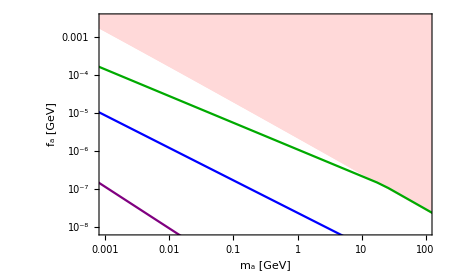

```mathematica
BulkAxion1=LogLogPlot[DecayConst1[x] ,{x,10^-5,10^4},PlotStyle->{ Darker[Green]} ];
BulkAxion2=LogLogPlot[  DecayConst2[x]  ,{x,10^-5,10^4},PlotStyle->{Purple} ];
BulkAxion3=LogLogPlot[ DecayConst3[x],{x,10^-5,10^4},PlotStyle->{Blue} ];
BulkAxion5=LogLogPlot[ DecayConst5[x],{x,10^-5,10^4},PlotStyle->{Green} ];
BulkAxion4=LogLogPlot[DecayConst4[x] ,{x,10^-5,10^4},PlotStyle->{Darker[Green]},PlotLegends->   { Placed[ LineLegend[{ Purple,Blue,Darker[Green]},{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics- }, LegendMarkerSize->{25,1.5},LabelStyle->{FontSize->1}],{0.8,.7}] }];
Show[qcdAxion,MaxAxionMassPlot,BulkAxion2,BulkAxion3,MaxAxionMassPlot,BulkAxion4,Frame->True,FrameStyle->Directive[Black,12,Thickness[0.0021]],ImageSize->450,Axes->False]
```

## Extra Dimension Model w/ axion from scalar

two KSVZ fermions

coefficient of the instanton computation

```mathematica
b0=7-4/3;
```

```mathematica
constScalar2=2* YukK/(24*Pi^2)*(1.5*10^-3)*Exp[8*.292] *3^(3-b0);
```

```mathematica
ma5dScalar2[Rinv_,ϵ_,fa_]:=Sqrt[constScalar2*ϵ^(3-b0)*Rinv^4*((2*Pi)/alphaQCDb[Rinv,b0,fa])^(9-b0)*Exp[(3*ϵ-1)*(2*Pi)/alphaQCDb[Rinv,b0,fa]]] /fa;
```

```mathematica
MaxAxionMass5dScalar[Rinv_,fa_]:= √YukK*((6*Pi)/alphaQCDb[Rinv,b0,fa]*Rinv)^2/fa  ;
```

Plots

```mathematica
DecayConstLimit=Interpolation[Table[ {MaxAxionMass5dScalar[10^7,10^x] , 10^-x},{x,-5,10,0.02}]];
```

```mathematica
DecayConst2=Interpolation[Table[{Min[MaxAxionMass5dScalar[10^6,10^x],ma5dScalar2[10^6,0.35,10^x]] , 10^-x},{x,-5,10,0.02}]]; 
DecayConst3=Interpolation[Table[{Min[MaxAxionMass5dScalar[10^7,10^x],ma5dScalar2[10^7,0.35,10^x]] , 10^-x},{x,-5,10,0.02}]];
DecayConst4=Interpolation[Table[{Min[MaxAxionMass5dScalar[10^7,10^x],ma5dScalar2[10^7,0.375,10^x]] , 10^-x},{x,-5,10,0.02}]];
MaTeX[5D, FontSize->18]
MaTeX[Scalar, FontSize->18]
```

-Graphics-

-Graphics-

```mathematica
qcdAxion=LogLogPlot[ x/0.005625 ,{x,10^-14,10^10},PlotStyle->Black  ,PlotRange->{{10^1,1.5*10^4},{10^-6.2,.10 }},Frame-> True, FrameTicks->ticksList,FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]},  PlotLabel->" (*GraphicsBox[{Thickness[0.021872265966754154`], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxllHtIU1Ecx7f5wiciPlZOt2vqfGw6d0eEGPutUFP/qDTMwhLzUaFlD41E
hXykf2gZ5jup6IEZSjNSlqEQZha+/rAotshICK0ZKRKRj3XPObtnVD84XD73
/u455/c9399hjhWl5tkJBAIhN1K5IeKGBcWtIOiPOn1XWB4CPBug6vN4hhw+
xWfpOpcZ6Lqz7en6eBhMomhgYAI9C8OhbO6XkXWVQe6RDwl2hkjo9VJ4HP8o
gbx8LkIVMIXztoBPQ/JX+2YF+d8shvEhwxVHvQIMabEZlnEbe5c2FU+98Cas
UsJxNM8XT5DcPBo+oVeCAMUlDxAj/qEEN51HcvuiC1SsxZ6ZXoiCfJzvCH4t
b5xPiFQwmKzf0VXqACb/8mx1i41z0H7DYih3L+yJsuxXw0LFfMGM2Q1W9fsK
OttYkA3dHsm76k05F9clodzzc/Hi5BkZNKYVB7dp1bD7WrVX/m8ZXX+4qHyp
w4chumZFQx/SJ5ABJSNdLUyPhoPOvnVslo2x3v3/814jV8A5G1fajzXGOKko
uyaElIgespQzZbrlnHUWEnvHugUPGEDya4Qa8v2sjfF+Y22M88MYKB7wWZv4
zgKLwo6BlFdOO2+MsaSOOSm881rRzbSqrXoEgAblXWfJ+W+KIRnlO2jAXHuq
Xl3mTbm9g4tDLpSx3ooNLdarSU15YnRX38kRFeWzvfWmEyoVWYe1aLGPJqPg
vbvJN++CPZjPcxtOUUKNX4XDyZfOUOO+91Hz/UgIWQle7HztAc11lw/PZkYS
/8h8QI/83hVB/JLgR/RNjSD7NW2Fmbfp5mhTuLUuf1Cg8xgMJ/P1SKFshTOA
MYzotSAj/n4SSnk/mu9xMOWS0cH4joAg4nd5IHlvCIRy1D/f/CinLc0ut+s8
KS/i+kVQH5c0lF/FWPUQkv6qDYVqVK+jkPSrWA7P60eqNPMCECM9g+RWPSxa
ngew3zco8/ry//O8PW44tTU7lLIc1Z0USBn7eFNC5yN9Lfn7fDjuwCEAnvn9
YR0SA6wsggOo7kop4HWc7az12zgjJEMy/UEK94zd8zGjDuTeSWFov5JzC6B+
Iyyh+vKMn8+klPn7DvtCz8C/9+EfIWg+wg==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGINIGYC4v21shbpIoYOLhOahdKslB1g/HBOsXbjeGWH
/uASlen8UPkqKP+9ASr/PIKv/qR53tlTBg4PXOMdZxUqO/D4r5+SusPAwRkk
/0vJodvrFYuJo4GDMQgIKzikxN5xY67Qc3Bfc3Q5ww45h7WqQAPe6sD54lOv
cGYs0oLzGUDggbrD+0XrFc5WKML5qWlAcEwNzt/q0PTouAXQHJCH2rUcZObF
aZ420HPwuTgx5t9iHTg/ISRIfQGnHpxfvFX092k+A4cfb18fsGzWdVh8fx/f
nGIDhy3mPw6ldGk7nAEBGQQfYo8+Bh9srqcWnF/326rgnIemg/cJdtvZrAYO
cstfeOj914CHB4z/51vpgzmJCH46yF/PDByqP20IyJbShPM36OUtZozRgvPB
/nyu4zClvTXqcoy+g66i/Jeca3oO56+GvdGfrQPnM3N2ySef04DzM/M/tJ6c
oupgAoqPYG04/0WW9rfpe9Xg/BkzgeCnIiTePmtAwiFHFm4+jP9l562uv60G
cD4sPe3Jr3k786qSA3p6AwAiSgd8
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}}}, {CompressedData["
1:eJxTTMoPSmViYGCwBGIQ/fdb6YM5hZYODCBgoOQA44NpQxWHx4kLr5nIY/L5
YwPuG6krwfm9Ed3+jB/kHYxBYLGFQ4xqhMy5GHmHTxsCsmelI/gOTY+Oz1ht
jsGvvv/jlnG3IpwfzinWbiyvDOfPWaS884+7Bpyvr7VS+MISLTg/PQ0Inmk7
qD5pnnf2lZnDm+Ktor+9dR16vF6xmDiaOdSAHFKl57BRL28xY42pg66i/Jec
a3oQfz8wgfO/7LzV9bfUGM4vXNN9O6PAyOF5lva36XN14Pz/IGCvBeefPgME
bzQcuN1US5l+GTlUg+y7peHgfYLddraoMZwPdk8ggg927y5jB7+LE2P+KWvC
+WD/qWjB+QkhQeoLOLUdltzfxzcn2djhCSjc87Xh5sP44PBnRvCjFRw/Jr8x
cmjh9V8/JVXb4fRhp7WZ94wcprS3Rl2O0XYoAQbTaTtjhxMg8Xm6DqBgTDMz
cfjx9vUBS2c9hxtCnxzPX0PwY0Dm7TGF83lAxu4wczi+a0cv2wYdOH89yOFr
NeH8mSAgqeHABQqfVaYOHvtrZS3YNRwOAKn0FBOHUyD796nD/TdjAn+V2Wo1
B/GpVzgznIwg/s9UhYT7e0NI+pivDOd323juSnNSgvND3l7+OINR3gEULWd6
jCF0jiwkvhtM4HxYeoDxv4LiP9XMIQUUDsvkHdRA4X/KzKH08DbXmXcVIfF0
2czBeUKzUJqXAsT9IeYOX/Z93Jq+TRbiDzkLVH4dgg/LX+5rji5n2CHngJ7/
AKbDnDY=
"], {{22.720299999999995`, 9.990630000000001}, {22.720299999999995`, 8.431249999999999}, {21.609399999999997`, 7.643750000000001}, {20.625, 7.643750000000001}, {19.729699999999998`, 7.643750000000001}, {19.029700000000002`, 8.306249999999999}, {19.029700000000002`, 9.129690000000002}, {19.029700000000002`, 9.667189999999998}, {19.262500000000003`, 10.617199999999997`}, {20.301599999999997`, 11.1906}, {21.162499999999998`, 11.6734}, {22.146900000000002`, 11.7453}, {22.720299999999995`, 11.781300000000002`}, {22.720299999999995`, 9.990630000000001}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIxIGYC4trfVgXnVtg6/AcDWQcYP0I1QubcHXkHE2Mg
aLaB8yXmxWmeLrBxAAkbCyvA+e8XrVc4W6EI55dsFf19+p2xw5PEhddM/K0c
YhQcPybvQfBvStckGrkaOzzP0v42PdYazr8u9MnxfJu1w0wQ0ETwwep8jeB8
mH0wvvK1R8EMMgoO+lorhS+UWMPdC7MPnQ/zr01lxArTvVYOIpWTSs6qyMHN
g/FngNzxE8GH+Q/GV3nSPO+slS2cjx6eAAqEnkI=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}}}, {CompressedData["
1:eJxTTMoPSmViYGCwBGIQLT71CmeGkLMDAwgYKDnA+H+/lT6YY6ji0O31isXk
pRMGnz824L6RuhKc3xvR7c/4Qd7BGARWOznEqEbInIuRdxD+5Hg+rRfB33mr
62+qPia/+v6PW8bdinB+OKdYu7G8Mpw/Z5Hyzj/uGnC+vtZK4QtLtOD89DQg
eKbtsKb7dgbDeUeHN8VbRX976zrc38c3x7jK0aHm04aA7Co9h89Aapa4o4Ou
ovyXnGt6DjNB4KQDnD/lG1v8DBEEfwnIAGV7h+dZ2t+mz9WB8/+DgL0WnH/6
DBC80XCwqYxYYbrW3qEaZN8tDYf631YF504g+GD3MDnA+atB7jV3cPC7ODHm
n7ImnA/2n4oWnJ8QEqS+gFPbIZvz54J0bgeHJ4kLr5nka8PNh/FTQeGwDcHv
DS5RmT7f3qGF13/9lFRthz+geJxo7zClvTXqcoy2w9IXHnr/P9o7nDjstDZz
nq4DyBtnShwcfrx9fcDSWc+BZfEkK8ajCP5xTatJp80d4Xx5x4/JZ7Y6Ohzf
taOXbYMOnL9e9UnzvLWacD44nCU1HObb6FyZpefo4LG/VtaCXcOhAhhcZ7sd
HE6B7N+nDvffjAn8VWar1Rx8TrDbzv5qB/F/pqqDCSh9LbaDpI/5ynB+t43n
rjQnJTg/5O3ljzMY5SHxJO8A8VeOLMQdMxF8WHqA8SeD4r/H0SEFFI7L5CHh
v9/RofTwNteZdxUd7JseHZ9x2NHBeUKzUJqXAsT9zE4OX/Z93Jq+TRYSHxkI
fi2IPwPBh+Uv9zVHlzPskHNAz38APMySjA==
"], {{35.42029999999999, 9.990630000000001}, {35.42029999999999, 8.431249999999999}, {34.309400000000004`, 7.643750000000001}, {33.324999999999996`, 7.643750000000001}, {32.42969999999999, 7.643750000000001}, {31.729699999999994`, 8.306249999999999}, {31.729699999999994`, 9.129690000000002}, {31.729699999999994`, 9.667189999999998}, {31.962499999999995`, 10.617199999999997`}, {33.00159999999999, 11.1906}, {33.862500000000004`, 11.6734}, {34.8469, 11.7453}, {35.42029999999999, 11.781300000000002`}, {35.42029999999999, 9.990630000000001}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYC4pKtor9P67k5ZOR/aD15RccBxq/5tCEg+5eu
g9Anx/NpT10d/nwrfTBno57Dzltdf1OnI/g9Xq9YTF66wPk+J9htZ891cdhi
/uNQCpeOwzwbnSuz2lwcEkKC1Bec1HJoWx5+yqgFkw/T/2Af3xzjKmeHMyDg
g+CfOOy0NjNO12EmCDC6wPm6Exb8MBRzcXDfXytroY7gP0lceM0kXxvOf79o
vcLZCkU4X/nao2AGGQUHlsWTrBh5XRwiVCNkzt2Rh9uHzv8PBrIOiYcva6du
dHYQqZxUclZFzkH1SfO8s1IucH4aCIQh+CElKtP/z0DwFRw/Jp/hdYXzKyJW
mJ71doWbD+PD7AeH3zKE+0yMgaAbk199/8ct425FOD8TFJ8l6nB+C6//+ilP
teDxBQ4/OT2HW9I1iUZTXeH8myD+UldU+a2ukHgV1YOkh6Ou8PQhiMYHh8ck
V4cZoHjaieBPncBfZXZaB84Hx897bUh47XOFuHOytkPdb6uCcw8Q/APAaE3/
g+DD0qcIyCNXEHxY+gUADk48HA==
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3169518292168768],ImageSize->{45.71760896637608, 23.511820672478205`},PlotRange->{{0., 45.720000000000006`}, {0., 23.51}}]) (*GraphicsBox[{Thickness[0.021344717182497336`], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJbIGYC4hZe//VTWvUc/oOBrAOMH6EaIXPujrzDi+Kt
or+5deB89/21shbLtTH41fd/3DLuVoTzrwt9cjxfZgTn35SuSTRyNYabB+PD
7EPnxyg4fkzeY+yQEnvHjfmHJpyfDOJbIPjMnF3yyXqaDp83BGTP2m7s0MBy
tN/wu4bD4bbl4aeKjB2cJzQLpVkpOvDHBtw3eq7oMBMEfgrB5SvB7haC6wfL
VwrBzXdfc3Q5ww8BON/EGAT+26PzYe6PBoVLDSfcPyXLSzb84+fG4MPCB8YH
G9OsBOeXHt7mOnOuIpwPC2+Yfeh8WPwd7N7XZPKYyUGkclLJWRU5B25HPq8Z
LzngfAYQaOCB89U/qbycxSkA5589AwQ8wnD+A9d4x1kbReDpA8aHp4/ax9nn
3/Bi8GHuh/Fh/oPxweFvZOzg/8TzkqkwH5wPtua+PNR+eQdhEC2i4CC7a8G+
1Dw5SDyqK8Dds/Lby4ozBQj+DFD87UTwla89CmY4g9APVv9BAW4+Eyj95GlC
4t0Tmr4qMPmw9A3jw/xrBPKXMIJf8wmUkNQw+DD3/P1W+mDORHV4+D6KEN9+
sUETzp8ygb/KrFsLzs/I/9B6coo2nL9W9UnzvF5dOB89/wIAaZSptA==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{23.921899999999994`, 11.334400000000002`}, {23.921899999999994`, 13.626599999999996`}, {22.2547, 15.4188}, {20.3031, 15.4188}, {18.349999999999998`, 15.4188}, {16.684399999999997`, 13.626599999999996`}, {16.684399999999997`, 11.334400000000002`}, {16.684399999999997`, 9.076559999999999}, {18.349999999999998`, 7.356249999999999}, {20.3031, 7.356249999999999}, {22.2547, 7.356249999999999}, {23.921899999999994`, 9.076559999999999}, {23.921899999999994`, 11.334400000000002`}}, CompressedData["
1:eJxTTMoPSmViYGCQBGIQnQYCx8wcRHu8XrF8UXOA8Vk4u+ST+1Qd7CojVpju
NXPwWHN0OUOGsgNImYmjmQMDCGxQdJCZF6d5+oCpw0wQ4FRwcGx6dHzGbxMH
d5D6HXIOL7K0v033RfC/7LzV9bfUGM4/fdhpbeY+I4czIBCj4KCvtVL4QoiR
Q7eN5660Q4oO4lOvcGY8MnQI5xRrN45XdthfK2uRfsXQ4VGE+PaLCapwPsz9
ML73CXbb2aUaDs9B9t81dPC/JV2TGKQFN/9J4sJrJu+1HaRB7t9gBFEnq+uw
5P4+vjnJxg4/3r4+YOmsB3c/jL9RL28xo4wpnM/jplrKdMrU4QTIH3G6Dimx
d9yYLcwcprS3Rl2W0YGH53rVJ83zcrXgfCmQvQIaDujhDwBVS6hT
"]}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}}}, {CompressedData["
1:eJxTTMoPSmViYGCQAmIQ7X2C3Xb2XgeH/2Ag6wDjR6hGyJy7I++gO2HBD0Mz
BH8mCCg6OOzNr3k7U1UBzi89vM115l1FOL9kq+jv0++MHf58K30wR9HOIUbB
8WPyHgT/pnRNopGrMcRefXs4fwZIf6Q9xBxNBP95lva36b5GcP5Wh6ZHxy10
HOpZjvYbuts7pKaBgI7DlAn8VWbddhB7Nuo5fNgQkD1L3BbOX3J/H98cZ2s4
H2xuraXDk8SF10zyteF80R6vVyxb1OD8bhvPXWlMSg48/uunpGpYO5wBgRxZ
iHte2sD5/cElKtPz7eB89be8+wws7R3uaMqu+S+s6FCwpvt2RgCUH4zgw9Sj
xwcATSbIVg==
"], CompressedData["
1:eJxTTMoPSmViYGAQAWIQXbCm+3ZGgL3DGRDwUXaA8WfMBAJLJYenWdrfpv+1
c3jgGu84y1HRYW+trEX6FDsH5wnNQmldCg48/uunpP6wdZDdtWBf6js5hxgF
x4/JMbYOJsZAMFnO4YZ0TaIRK4KfDzK/wQbOB9OLrRxS0oBgmTycP2MCf5XZ
ajU4X2ZenObpDboODSxH+w232zicOOy0NlNOD0Lr2cL5f76VPpjDaAfnTwWb
Y+dwfNeOXjYDXQd9rZXCF0TsHdJB9j3Thvu3hRfoEVUEPyEkSH0BJ4IP1pei
5YAeXgC79oGj
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQAGIQ/WlDQPaseheHU4ed1mb+U3eA8Vt4/ddPWartUBGx
wvQss4uDrqL8l5xreg7paUDwzwnOz+b8uSCdG8FXf9I876yXo0NK7B03Zgtt
OP9p4sJrJufV4Hz+2ID7RupKDlO+scXPUHFyOAMCObIOn0H2izvD+TxAZ6RK
uMD5Qp8cz6fVujgYg0CzEpxvAuI7K8P5dzRl1/xvVnb4E5N79F8WAX4Ugu+q
Wso0K8LF4YFrvOOsQmWHnbe6/qb6Q+1jVnZgWTzJilEWyp+s4LCm+3YGw3xn
B/c1R5cz7JCDuF8dwQerP+oE54tPvcKZkQTlWyjA/V99/8ct49OKDsIg9991
dAjnFGs3nq8M509pb426vEcVzp8xgb/KLFvdARQdaWUucD4s/k7s2tHLNgHB
lwDZuwjBh8U3AMCs3Do=
"], {{40.02969999999999, 11.9781}, {35.7484, 11.9781}, {35.8734, 14.557799999999999`}, {37.25309999999999, 15.131299999999996`}, {37.9703, 15.131299999999996`}, {39.1875, 15.131299999999996`}, {40.012499999999996`, 13.9844}, {40.02969999999999, 11.9781}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIxIGYC4gjx7RcZ1rk5/AcDWQcYP0I1QubcHXkHE2Mg
kEbwl73w0Psv6OYAEjYWVoDz3y9ar3C2QhHOL9kq+vv0O2OHHq9XLCaMrg4x
Co4fk/cg+DelaxKNXI0deP3XT0ntQPBZFk+yYpzr6jATBDQR/OdZ2t+m+xrB
+TD7YHzla4+CGWQUHDbq5S1mnOIKdy/MPnQ+zL8W147mmli4OohUTio5qyIH
Nw/GTwOBawg+zH8w/pru2xkM5Qg+engCAOIukE0=
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3169518292168768],ImageSize->{46.853858032378575`, 23.511820672478205`},PlotRange->{{0., 46.849999999999994`}, {0., 23.51}}])"];
```

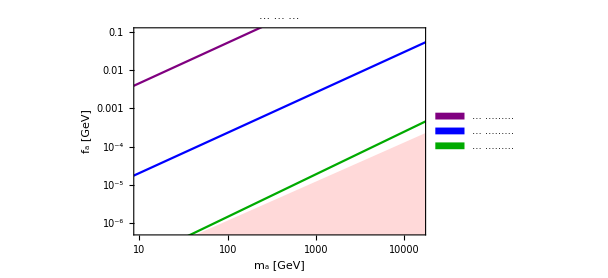

```mathematica
BulkAxion1=LogLogPlot[DecayConstLimit[x] ,{x,10^-5,10^8},PlotStyle->LightRed, Filling->Bottom, FillingStyle->LightRed];
BulkAxion2=LogLogPlot[  DecayConst2[x]  ,{x,10^-8,10^8},PlotStyle->{Purple} ];
BulkAxion3=LogLogPlot[ DecayConst3[x],{x,10^-5,10^8},PlotStyle->{Blue} ];
BulkAxion4=LogLogPlot[DecayConst4[x] ,{x,10^-5,10^8},PlotStyle->{Darker[Green]},PlotLegends->   { Placed[ SwatchLegend[{  Purple,Blue,Darker[Green]},{(*"(*GraphicsBox[{Thickness[0.028384899233607718`], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJ+KC1cOank7BMlhz35NW9nHlVygPFdJjQLpVkpO5w9
AwQ1CP5913jHWYoI/lavDRZzLBng/BbxWtbMY3/tYXzxJpkpBsG/MPjK1x4F
M5xRgvPd1xxdzhCh5OD7xPOS6eS/cD7MfBgfZj+Mzx8bcN+oHMGHuR+dj+6/
HcFWEf+Xy8D5vRHd/owTZOH+hfFh9sH4MPfA+DD/wvgw/6DzWxXYVc9skYHz
a+7/uGV8WhruXxgfZj6MD7Mfxof5F8aHuR+dD/MfAH4hyWs=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJJKC09L07z9AEjh3BOsXZjeyUHGP/C1bA3+tYqDn+/
lT6Ys9HIYYv5j0MpWmoOxiDgDJX/re7wZeetrr9HDR1aWI72G37XdJgJAi8N
HJ5naX+bXqvl4H9xYsy/YARfX2ul8AUXfTg/4JZ0TeIkXYc3xVtFf5/WdDi+
a0cv2wYdBymQOy6oQ9Sz6Dg8TVx4zcRfzWHOIuWdf45rO4j2eL1iuaIC58Pc
D+O/acvtNrot7+APMv+TtsNaIR2+9DgZBxbOLvnkczoQd/6UcHgKcsdeXQe3
NUeXM0SIOvx5+/qAZbK+wwPXeMdZhiKQ8AgwgPNVnzTPOxtlCOcvvr+Pb85n
QweFXQv2pa4Tc4hWcPyY7GPk0KrArnqmRBKifpeRg/onlZezOGXh4at87VEw
wx0FB/Tw5/VfPyX1hqHD+0XrFc52IPhrQO5/pwDng/1nLedwXeiT4/ltUPcE
SkPsrzF06Ivo9mcUEHNwbHp0fMZuA4c0EFAThfsHxn8B8v9dfTj/KCj8A/Qc
DnbvazJhFnPYoJe3mPGOrsMMUHhZSjtsdwAZqOvwZd/HrelicnA+zD8wPsz9
MP6pw05rM+tU4PxfoHB2VnOo+bQhIPuXrsMrUPyvVneQmHqFMyNJz6EZ5FFX
TYj8LH2HHyD1zFpw98P4BqD0cQTBTwf5o8zQQVdR/ktOmaZD4Zru2xkbDB0a
flsVnMtQR4QfyD5uNTgfLK+hghH+AI32XVo=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{21.498400000000004`, 5.8734399999999996`}, {21.498400000000004`, 6.2203100000000004`}, {21.2125, 6.4593799999999995`}, {20.924999999999997`, 6.4593799999999995`}, {20.5781, 6.4593799999999995`}, {20.339100000000002`, 6.17188}, {20.339100000000002`, 5.885939999999999}, {20.339100000000002`, 5.539059999999999}, {20.626599999999996`, 5.300000000000001}, {20.912499999999998`, 5.300000000000001}, {21.2594, 5.300000000000001}, {21.498400000000004`, 5.5874999999999995`}, {21.498400000000004`, 5.8734399999999996`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxd1HlIFFEcB/AxBesPDUzbPDZWZ9fdtdI8cg4NfhZrqZFLl0tuh3lVRnek
tVZ22B8raZC3BB2wCZkSWRKxprKYul5ZhiIoQuQZKiGSmO1747wBf/CY/TDM
m9/+vo/xP3XhQLozRVFOjqVzrDWO9Y5ZaE4bjAIK1Uk5iDZHx33MGFVA2rGh
WOcFHm4OLwyGVwaArPjbutNfOQhH5UyDUREzmzrEg7J/9CBVRcNMnT6r4mEU
mOYcP46qiPE+rJq4+/uRqRBfLdhRFfDw6+yW+dLcIGjMlbOZaRwxfl8YS4z7
1DOQu8hf7FqrJcZ9x6uJ47+47qw8HAhX670WO94wsL/3sfEfHSi8b2iV/Vji
DFyssM8dyWL/ontQ/4tq8rzP0+PaDr0GylENMMR5LrbC0FbJBfETLhFNkvG+
DQyUFq2/EZmggWQ0z62s4EktwN3R1rIEjrgEXZMlL6NqlPzDYy6mO5+HnynP
+iMKJYv9i/47PfmZawlcmSsv/I9zKggJqt7Qo+Thvlti7ZN0JWim3azb2ziY
eV6r6DTQYEb9p3CQjsYQS0Nby66aM+6cMC+goTnfktT+loXrLe915dtouILm
f4uFPa9tFkpDC3leZmFYdyKmwl/y7qJ7HhkTAcT4+ZoAsIztDV7Ok4xzb5CM
c9ZxxGVo/nE8cZLsQy9l5aF6fjzbTvkTm9B5zpITa+aU4xVameDfHBhVBr8u
kxekorkZJA/4mlLCbCwxPnftDPyxztZnlmyEpflrI1WXGOH+J294OWx1r+pj
hJxue5N88X2jD/EDhavK7ulHrEPzypZDXfD5F05TzEo+m4XzVyIZX/dJHkN5
LkXCoem+2bImOXGhwZzoNONL/Ai5Tibk78bCCMoj1JPkKzo6x/BqRydPLH4f
ctD8zJtg9ffjPx9/1nY=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx1lHtIU2EYxmcGSzID87K8bR4V2ywxXQXiOXsktEjDysiTWGK1KZat0kJL
CKxcNA0Lxdsoy8IgSyFMEllISZFzYpqFCUoYRGmpmQSadi7uO1j4wvfH7/C9
t+d9zxd4xLhP7yyTyZy4k8CdFdwxNaS8iewHlG11Vr09AA5OcfEyReko9BrT
5faDQLnpSmqfJRjeFf0uWWd0hHf33kibf8EQ/pwdNlNJM+J352CkeLf2yr7T
mLjbpOpmgwhXlq09vzVhA+Zmzo5YTjNIfC2na3+FIk0VO3l0iMFoxp0B7Y9Q
8f68xPnsgy3dYSDc8GVn+EI1xHjf1IRHWM4RGsKtKPr0itXgofljlqwSOHZo
KN45XwMll85Wujz/bN5zvMYksaBHAacXHzhdI+oVDIzltnjOdqnFPlp0KJzi
HNvUmH42eO2PXmKhPwuzlF0ZeJTs+rpSqxH1fUvj8pqkpnK9Bjbe2mmSP5HX
9cnyXMHrUPs/a6M4S5ZYceuwumtCTXhHY2eD7ANFeHvZJXdDtsTtxsLx6jgK
C7w9l1iYQ4/EjvovDP8ejEqgFvPQWFdwM6+7nMI796nYnngGMt7KgqA3cDbA
QMH7Udz+8PGMOsIXZ6NP2VeBsCsvSwSQyfvNUKI+McAj941umdcpCGM4ALHO
24HYNtCZo2Uh5s9TERb6VSgJC3XE+xMW4pb4YB1XrmETYBBMIe7fakDF/y+P
vWBs5BaqToe0ENbPXuiJqmrO1kss1JHEEBb6uUqjw2wt0tZ74z6/n3tp8Z7S
F8IaZNBoTY5mF+S+uDdsdbPk0hgrzjFHzvrgZTG3cEUSv+f1fCqxkN+FwbR1
siXznO9S9vInLPR3IoDMr5Q1JzlFKEl8BzeHn6x3SpRY2Ne5GOwf75us6ggg
7MHrO+pHuFglD7H1K0S20RiJS4+t2eyx2KeOsGN+Dna8P6m8Xu0K/Ps+/QW/
mRC9
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{35.22899128268991, 16.338709838107096`},PlotRange->{{0., 35.230000000000004`}, {0., 16.34}}]) ",*)"(*GraphicsBox[{Thickness[0.021008403361344536`], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJ+KL3DoenR8R2qDlvMfxxK6VJ1gPH/fit9MEdQzUFu
+QsPPXsEX7TH6xXLFRU4fyYYMML56p9UXs7iZIDzWfV/cV3i+WOPlT9RFc5P
CAlSX8Cp6nDh97Hr827+h/Nh5sP4MPth/JTYO27MFqpwPsz96Hx0/zlPaBZK
i1KA8x+4xjvOeqgA9y+MD7MPxoe5B8aH+RfGh/kHnb/y28uKMwkIvokxEGyW
h/sXxoeZD+PD7IfxYf6F8WHuR+fD/AcAO6nQPA==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJJKD0huERl+n5ThzMg8EbFAcZ/kaX9bbqtOoRea+rw
HwTqNR1sKyNWmOqaOsgsf+GhN1/bQfVJ87yzs0wcju/a0cv2QddhJhgYQ8zr
0YPIvzKC8x2aHh2fIY3gR4hvv8ggZ+jwFGTPXl0HbjfVUqZZBhD5HG2HLztv
df01NXCYPoG/ymy1poP41CucGUIGDsfA9qnD+TD3w/jvF61XOGuhBNGnbeAQ
zinWbqyv4LBBL28x4xoDhx3BVhH/02UcGlmO9huaGzpU3f9xy1hbwuE5yB26
Rg5tCuyqZ66IQeSfI/gQ95rA+QVrum9nXDBxeNOW2220W9IhJfaOG7OFqcOX
fR+3pn+TceDxXz8ldYepgzEITFaAh28EyD3+yg7o4V8IMm+DicOvt68PWDqr
wvl3NGXX/E9WhvP35Ne8nemq6FD326rgXIeJg0jlpJKzKvION6VrEo1cTRyC
3l7+OINR0sH/4sSYf8nGDg9c4x1nfRSH+wfG19daKXyhBMGHxIshxL2fJRw0
3vLuM/A0dNgOCi92eYc/30ofzFE0dGAAAQNFOB/mHxgf5n4YH2KuOpw/pb01
6vIcTUj6iDKExJuTtsPnDQHZs6YbOjwABbSCLiQ+fI0cThx2Wpv5Txfufhi/
ZKvo79N5xnB+JCh+7EwcZoCSYaSuwwpgMv3fCAyfHq9XLF+04OE3GWR/jCac
3wAKRw11jPAHAE7Aa/4=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{24.865599999999997`, 6.668749999999999}, {24.865599999999997`, 7.0734400000000015`}, {24.531299999999998`, 7.353129999999999}, {24.196899999999996`, 7.353129999999999}, {23.7922, 7.353129999999999}, {23.5141, 7.018750000000001}, {23.5141, 6.68281}, {23.5141, 6.27969}, {23.848399999999998`, 5.999999999999999}, {24.1828, 5.999999999999999}, {24.5875, 5.999999999999999}, {24.865599999999997`, 6.334379999999999}, {24.865599999999997`, 6.668749999999999}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJXIGYC4snf2OJn6Dg4CFdOKjl7RMEBxk9PA4IwZQeZ
eXGapwPsHVJi77gxR6g6bDH/cSjll63D32+lD+ZcVHWQAMkb2Dv4XpwY869Z
zaH2t1XBuR/2DutVnzTP69WA82s+bQjI3qUF57Nwdsknv9Nx8AHpu2zncAYE
evQcZswEgkpbOF9fa6XwBREbOD9GwfFjMo81RN1NHTj/+K4dvWwXtOD8gFvS
NYmbNB2mT+CvMqu2dtju0PToeIUmxL0bEHx7IDXjN4Lf4/WKxSTQxsEf5K7H
CD7M/TC+zPIXHnrzteH6f7x9fcCSWcfBpjJihelaBP8DUNus6Qh+wZru2xkT
EHyfE+y2s1utHbbo5S1m/KPt8DRL+9t0XhsHU5u9QdMe6jrYgsyLtYXzS7aK
/j6dh+DrgsLnCYIPDqczdg46ivJfcsoQfJj7YXwTYxDQclgK9Mb/g3YOP0Hu
WazhAIq2s1F2DsdA4Vmg7tAfXKIy/b0txJ2mag5fd97q+ltq68AAAgpqEHFR
W4cdoPCTUIOkj1U2kPTArOYQLr79IkOejcOU9taoy39UHXpB5sXbQPR9RfAz
8z+0ntyC4G8AOSRX1eEPKJ0VovE3Ivhg94TawvmQ8LSD88HxwWsPTVfKcL7y
tUfBDGcU4Hz1TyovZ3lKQdwvZefwed/HrelhEg5TQekn2xbO/w8C+23gfHD6
mm3tsF5Ihy99nqTDkvv7+OYYW0PC2UfW4QvIfUutHURA+YtFFh6/qaD8xSYH
59/WlF3zn1kBzgdHz2UFB/GpVzgzDlk7dNt47kpLUnQ4cdhpbWYcgl8Pyk8c
CP4GUDpaY+WwFuSefwpw/hoQ/548nA/O38+kIOHy0tqhTYFd9cwVMXj8wvhP
EhdeM5G3h/Nh5cOOYKuI/8+lHdDLDwDzzu42
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11G1IU1EYAOD5kWJkRVKmzn3U5pC1lZuirUnvucvMjBpWaqTZqm2WmP5Q
IlIKNINWNNTSTbGVwf4IGVSm6ZRkKX7MwhlhwigMJOcPPxiWmu3e684loxcO
l4d7zz3nvOc9h3+hKEMbwGKx/Lwt3dv8vW2IjEoV3HAtjssb+OAz9XQLIDu8
7SPLQ0B/x5v7Qa0iCH/oDMlXMK71BOXVOxG2xGhZjKtCMHVF7KlbiYG+WEX1
YBaCY/3ByQ0JjF9Krzb7LYuhuzw6Sf8MwaXcicMB9WJYyim0//6GgN10LnbQ
KIbHyj1Os4fxphPPa7U9BPbNJUWxA1SQoOzKePRVgl0Z6v0wRfr3e40UwubQ
iC557f1tKbhDbftMMsbT61wQ8tOiF69zlArKyf/mS6F9/O6Kto2A7+R6uyQw
WpQX7NAQ0Ph0d/uyVUJ/L2dMjd+FsE1kXEZwK9D+IC5RCvOt6gJzKoI+Mp/F
UpCTcQDh8blo9uJQwv9N9Rf965GxTPfes4yp+U9JsFlkWITY0dapI1Iu4+33
jv4IXBBAYHO1wi+ZMTV+CmPf/D+Q4y0J6PWdQRBJ7pdaSOfDsFYPpTF0/lyI
3h++CFKEpf7mJAJ7UvPkU3wd43Syn52AXzPTPft7hfCCrCMnAedPZYgsaUK6
PucIiKcSJ4A71qwB2QIBnUVlM6axXdhanTfe87G35KpdsjYe9sqqNw5ywGXb
3Ch/R0COMJvt6IwC4WRF07CZAHdVoUH2NgK+RJVpZKcJmLfNvtJn7qTrNYgx
VX9GhE2dKzaC1Ba7lfU5EmrI87MMUEaev2kOvb4NCLgdFpvWwaHrfSui59PN
AYM3zfERjKl8JzKmzpd+rf9xLrbKWLFNZ+ZhG5RpHboLfLx/YderS4adfPx/
n0+WCOpWFwGbOi8DABOx0S2rNYyv9b5OMZXzsKl8Kdn0/hxCUMULFg45d9D5
3Ehg+/bPZ9/9o54Zna3ns2H9/fQHjSMVgQ==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJJKK07YcEPQzZ3hzMg8EbFAcZ/kaX9bbqtusNN6ZpE
o79uDv9BoF7TgWXxJCvGvW4OMstfeOjN13aojFhherbYzeH4rh29bB90HUyM
geCzK8S8Hj2I/GwEv215+CkjEwRf5JPj+bStLg5PQfbt1XXI4fy5IL3YBSKf
o+2QePiydqqji8P0CfxVZqs1HT5tCMiepe/icAxsnzqcD3M/jP9+0XqFsxZK
Dhv18hYz2rg4hHOKtRvrKzgcqJW1SK9xcdgRbBXxP13GYQXQG/8PujhU3f9x
y1hbAuJfW1eHNgV21TNXxByWgeRnIvhg95q6wfkLbHSuzOpzc3jTlttttFvS
QWLqFc6MQ24OX/Z93Jr+TcbhDe8+g5lM7g6gYDGerAAP3wiQe/yVHdDDfx7I
vDo3h19vXx+wdFaF8+9oyq75n6wM5+/Jr3k701XRQe1J87yzWW4OIpWTSs6q
yDuElKhM/+/h5hD09vLHGYySDjz+66ek3nB1eOAa7zjrozjcPzB+3W+rgnMJ
CD7EHS4Q936WcPgTk3v03ykXh+2g8GKXd3iSuPCayXYXBwYQMFCE82H+gfFh
7ofxIfGtDudPaW+NujxHE5I+Lrs4iIPCzUnb4cE+vjnGn1wcHkSIb7+ooAuJ
D19XhxOHndZm/tOFux/GV3D8mHzmLoIvBIofVzeHGTOBIFLXYeetrr+p6cDw
6fF6xfJFCx5+k0H2x2jC+Q2gcNBQxwh/AAoebrI=
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32127889429728423`],ImageSize->{47.59699128268991, 18.729753424657535`},PlotRange->{{0., 47.6}, {0., 18.73}}]) ","(*GraphicsBox[{Thickness[0.021008403361344536`], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJ+KL3DoenR8R2qDlvMfxxK6VJ1gPH/fit9MEdQzUFu
+QsPPXsEX7TH6xXLFRU4fyYYMML56p9UXs7iZIDzWfV/cV3i+WOPlT9RFc5P
CAlSX8Cp6nDh97Hr827+h/Nh5sP4MPth/JTYO27MFqpwPsz96Hx0/zlPaBZK
i1KA8x+4xjvOeqgA9y+MD7MPxoe5B8aH+RfGh/kHnb/y28uKMwkIvokxEGyW
h/sXxoeZD+PD7IfxYf6F8WHuR+fD/AcAO6nQPA==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJJKD0huERl+n5ThzMg8EbFAcZ/kaX9bbqtOoRea+rw
HwTqNR1sKyNWmOqaOsgsf+GhN1/bQfVJ87yzs0wcju/a0cv2QddhJhgYQ8zr
0YPIvzKC8x2aHh2fIY3gR4hvv8ggZ+jwFGTPXl0HbjfVUqZZBhD5HG2HLztv
df01NXCYPoG/ymy1poP41CucGUIGDsfA9qnD+TD3w/jvF61XOGuhBNGnbeAQ
zinWbqyv4LBBL28x4xoDhx3BVhH/02UcGlmO9huaGzpU3f9xy1hbwuE5yB26
Rg5tCuyqZ66IQeSfI/gQ95rA+QVrum9nXDBxeNOW2220W9IhJfaOG7OFqcOX
fR+3pn+TceDxXz8ldYepgzEITFaAh28EyD3+yg7o4V8IMm+DicOvt68PWDqr
wvl3NGXX/E9WhvP35Ne8nemq6FD326rgXIeJg0jlpJKzKvION6VrEo1cTRyC
3l7+OINR0sH/4sSYf8nGDg9c4x1nfRSH+wfG19daKXyhBMGHxIshxL2fJRw0
3vLuM/A0dNgOCi92eYc/30ofzFE0dGAAAQNFOB/mHxgf5n4YH2KuOpw/pb01
6vIcTUj6iDKExJuTtsPnDQHZs6YbOjwABbSCLiQ+fI0cThx2Wpv5Txfufhi/
ZKvo79N5xnB+JCh+7EwcZoCSYaSuwwpgMv3fCAyfHq9XLF+04OE3GWR/jCac
3wAKRw11jPAHAE7Aa/4=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{24.865599999999997`, 6.668749999999999}, {24.865599999999997`, 7.0734400000000015`}, {24.531299999999998`, 7.353129999999999}, {24.196899999999996`, 7.353129999999999}, {23.7922, 7.353129999999999}, {23.5141, 7.018750000000001}, {23.5141, 6.68281}, {23.5141, 6.27969}, {23.848399999999998`, 5.999999999999999}, {24.1828, 5.999999999999999}, {24.5875, 5.999999999999999}, {24.865599999999997`, 6.334379999999999}, {24.865599999999997`, 6.668749999999999}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJXIGYC4snf2OJn6Dg4CFdOKjl7RMEBxk9PA4IwZQeZ
eXGapwPsHVJi77gxR6g6bDH/cSjll63D32+lD+ZcVHWQAMkb2Dv4XpwY869Z
zaH2t1XBuR/2DutVnzTP69WA82s+bQjI3qUF57Nwdsknv9Nx8AHpu2zncAYE
evQcZswEgkpbOF9fa6XwBREbOD9GwfFjMo81RN1NHTj/+K4dvWwXtOD8gFvS
NYmbNB2mT+CvMqu2dtju0PToeIUmxL0bEHx7IDXjN4Lf4/WKxSTQxsEf5K7H
CD7M/TC+zPIXHnrzteH6f7x9fcCSWcfBpjJihelaBP8DUNus6Qh+wZru2xkT
EHyfE+y2s1utHbbo5S1m/KPt8DRL+9t0XhsHU5u9QdMe6jrYgsyLtYXzS7aK
/j6dh+DrgsLnCYIPDqczdg46ivJfcsoQfJj7YXwTYxDQclgK9Mb/g3YOP0Hu
WazhAIq2s1F2DsdA4Vmg7tAfXKIy/b0txJ2mag5fd97q+ltq68AAAgpqEHFR
W4cdoPCTUIOkj1U2kPTArOYQLr79IkOejcOU9taoy39UHXpB5sXbQPR9RfAz
8z+0ntyC4G8AOSRX1eEPKJ0VovE3Ivhg94TawvmQ8LSD88HxwWsPTVfKcL7y
tUfBDGcU4Hz1TyovZ3lKQdwvZefwed/HrelhEg5TQekn2xbO/w8C+23gfHD6
mm3tsF5Ihy99nqTDkvv7+OYYW0PC2UfW4QvIfUutHURA+YtFFh6/qaD8xSYH
59/WlF3zn1kBzgdHz2UFB/GpVzgzDlk7dNt47kpLUnQ4cdhpbWYcgl8Pyk8c
CP4GUDpaY+WwFuSefwpw/hoQ/548nA/O38+kIOHy0tqhTYFd9cwVMXj8wvhP
EhdeM5G3h/Nh5cOOYKuI/8+lHdDLDwDzzu42
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11G1IU1EYAOD5kWJkRVKmzn3U5pC1lZuirUnvucvMjBpWaqTZqm2WmP5Q
IlIKNINWNNTSTbGVwf4IGVSm6ZRkKX7MwhlhwigMJOcPPxiWmu3e684loxcO
l4d7zz3nvOc9h3+hKEMbwGKx/Lwt3dv8vW2IjEoV3HAtjssb+OAz9XQLIDu8
7SPLQ0B/x5v7Qa0iCH/oDMlXMK71BOXVOxG2xGhZjKtCMHVF7KlbiYG+WEX1
YBaCY/3ByQ0JjF9Krzb7LYuhuzw6Sf8MwaXcicMB9WJYyim0//6GgN10LnbQ
KIbHyj1Os4fxphPPa7U9BPbNJUWxA1SQoOzKePRVgl0Z6v0wRfr3e40UwubQ
iC557f1tKbhDbftMMsbT61wQ8tOiF69zlArKyf/mS6F9/O6Kto2A7+R6uyQw
WpQX7NAQ0Ph0d/uyVUJ/L2dMjd+FsE1kXEZwK9D+IC5RCvOt6gJzKoI+Mp/F
UpCTcQDh8blo9uJQwv9N9Rf965GxTPfes4yp+U9JsFlkWITY0dapI1Iu4+33
jv4IXBBAYHO1wi+ZMTV+CmPf/D+Q4y0J6PWdQRBJ7pdaSOfDsFYPpTF0/lyI
3h++CFKEpf7mJAJ7UvPkU3wd43Syn52AXzPTPft7hfCCrCMnAedPZYgsaUK6
PucIiKcSJ4A71qwB2QIBnUVlM6axXdhanTfe87G35KpdsjYe9sqqNw5ywGXb
3Ch/R0COMJvt6IwC4WRF07CZAHdVoUH2NgK+RJVpZKcJmLfNvtJn7qTrNYgx
VX9GhE2dKzaC1Ba7lfU5EmrI87MMUEaev2kOvb4NCLgdFpvWwaHrfSui59PN
AYM3zfERjKl8JzKmzpd+rf9xLrbKWLFNZ+ZhG5RpHboLfLx/YderS4adfPx/
n0+WCOpWFwGbOi8DABOx0S2rNYyv9b5OMZXzsKl8Kdn0/hxCUMULFg45d9D5
3Ehg+/bPZ9/9o54Zna3ns2H9/fQHjSMVgQ==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJJKK07YcEPQzZ3hzMg8EbFAcZ/kaX9bbqtusNN6ZpE
o79uDv9BoF7TgWXxJCvGvW4OMstfeOjN13aojFhherbYzeH4rh29bB90HUyM
geCzK8S8Hj2I/GwEv215+CkjEwRf5JPj+bStLg5PQfbt1XXI4fy5IL3YBSKf
o+2QePiydqqji8P0CfxVZqs1HT5tCMiepe/icAxsnzqcD3M/jP9+0XqFsxZK
Dhv18hYz2rg4hHOKtRvrKzgcqJW1SK9xcdgRbBXxP13GYQXQG/8PujhU3f9x
y1hbAuJfW1eHNgV21TNXxByWgeRnIvhg95q6wfkLbHSuzOpzc3jTlttttFvS
QWLqFc6MQ24OX/Z93Jr+TcbhDe8+g5lM7g6gYDGerAAP3wiQe/yVHdDDfx7I
vDo3h19vXx+wdFaF8+9oyq75n6wM5+/Jr3k701XRQe1J87yzWW4OIpWTSs6q
yDuElKhM/+/h5hD09vLHGYySDjz+66ek3nB1eOAa7zjrozjcPzB+3W+rgnMJ
CD7EHS4Q936WcPgTk3v03ykXh+2g8GKXd3iSuPCayXYXBwYQMFCE82H+gfFh
7ofxIfGtDudPaW+NujxHE5I+Lrs4iIPCzUnb4cE+vjnGn1wcHkSIb7+ooAuJ
D19XhxOHndZm/tOFux/GV3D8mHzmLoIvBIofVzeHGTOBIFLXYeetrr+p6cDw
6fF6xfJFCx5+k0H2x2jC+Q2gcNBQxwh/AAoebrI=
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32127889429728423`],ImageSize->{47.59699128268991, 18.729753424657535`},PlotRange->{{0., 47.6}, {0., 18.73}}]) ","(*GraphicsBox[{Thickness[0.021008403361344536`], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJ+KL3DoenR8R2qDlvMfxxK6VJ1gPH/fit9MEdQzUFu
+QsPPXsEX7TH6xXLFRU4fyYYMML56p9UXs7iZIDzWfV/cV3i+WOPlT9RFc5P
CAlSX8Cp6nDh97Hr827+h/Nh5sP4MPth/JTYO27MFqpwPsz96Hx0/zlPaBZK
i1KA8x+4xjvOeqgA9y+MD7MPxoe5B8aH+RfGh/kHnb/y28uKMwkIvokxEGyW
h/sXxoeZD+PD7IfxYf6F8WHuR+fD/AcAO6nQPA==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgAmJJKD0huERl+n5ThzMg8EbFAcZ/kaX9bbqtOoRea+rw
HwTqNR1sKyNWmOqaOsgsf+GhN1/bQfVJ87yzs0wcju/a0cv2QddhJhgYQ8zr
0YPIvzKC8x2aHh2fIY3gR4hvv8ggZ+jwFGTPXl0HbjfVUqZZBhD5HG2HLztv
df01NXCYPoG/ymy1poP41CucGUIGDsfA9qnD+TD3w/jvF61XOGuhBNGnbeAQ
zinWbqyv4LBBL28x4xoDhx3BVhH/02UcGlmO9huaGzpU3f9xy1hbwuE5yB26
Rg5tCuyqZ66IQeSfI/gQ95rA+QVrum9nXDBxeNOW2220W9IhJfaOG7OFqcOX
fR+3pn+TceDxXz8ldYepgzEITFaAh28EyD3+yg7o4V8IMm+DicOvt68PWDqr
wvl3NGXX/E9WhvP35Ne8nemq6FD326rgXIeJg0jlpJKzKvION6VrEo1cTRyC
3l7+OINR0sH/4sSYf8nGDg9c4x1nfRSH+wfG19daKXyhBMGHxIshxL2fJRw0
3vLuM/A0dNgOCi92eYc/30ofzFE0dGAAAQNFOB/mHxgf5n4YH2KuOpw/pb01
6vIcTUj6iDKExJuTtsPnDQHZs6YbOjwABbSCLiQ+fI0cThx2Wpv5Txfufhi/
ZKvo79N5xnB+JCh+7EwcZoCSYaSuwwpgMv3fCAyfHq9XLF+04OE3GWR/jCac
3wAKRw11jPAHAE7Aa/4=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{24.865599999999997`, 6.668749999999999}, {24.865599999999997`, 7.0734400000000015`}, {24.531299999999998`, 7.353129999999999}, {24.196899999999996`, 7.353129999999999}, {23.7922, 7.353129999999999}, {23.5141, 7.018750000000001}, {23.5141, 6.68281}, {23.5141, 6.27969}, {23.848399999999998`, 5.999999999999999}, {24.1828, 5.999999999999999}, {24.5875, 5.999999999999999}, {24.865599999999997`, 6.334379999999999}, {24.865599999999997`, 6.668749999999999}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJXIGYC4snf2OJn6Dg4CFdOKjl7RMEBxk9PA4IwZQeZ
eXGapwPsHVJi77gxR6g6bDH/cSjll63D32+lD+ZcVHWQAMkb2Dv4XpwY869Z
zaH2t1XBuR/2DutVnzTP69WA82s+bQjI3qUF57Nwdsknv9Nx8AHpu2zncAYE
evQcZswEgkpbOF9fa6XwBREbOD9GwfFjMo81RN1NHTj/+K4dvWwXtOD8gFvS
NYmbNB2mT+CvMqu2dtju0PToeIUmxL0bEHx7IDXjN4Lf4/WKxSTQxsEf5K7H
CD7M/TC+zPIXHnrzteH6f7x9fcCSWcfBpjJihelaBP8DUNus6Qh+wZru2xkT
EHyfE+y2s1utHbbo5S1m/KPt8DRL+9t0XhsHU5u9QdMe6jrYgsyLtYXzS7aK
/j6dh+DrgsLnCYIPDqczdg46ivJfcsoQfJj7YXwTYxDQclgK9Mb/g3YOP0Hu
WazhAIq2s1F2DsdA4Vmg7tAfXKIy/b0txJ2mag5fd97q+ltq68AAAgpqEHFR
W4cdoPCTUIOkj1U2kPTArOYQLr79IkOejcOU9taoy39UHXpB5sXbQPR9RfAz
8z+0ntyC4G8AOSRX1eEPKJ0VovE3Ivhg94TawvmQ8LSD88HxwWsPTVfKcL7y
tUfBDGcU4Hz1TyovZ3lKQdwvZefwed/HrelhEg5TQekn2xbO/w8C+23gfHD6
mm3tsF5Ihy99nqTDkvv7+OYYW0PC2UfW4QvIfUutHURA+YtFFh6/qaD8xSYH
59/WlF3zn1kBzgdHz2UFB/GpVzgzDlk7dNt47kpLUnQ4cdhpbWYcgl8Pyk8c
CP4GUDpaY+WwFuSefwpw/hoQ/548nA/O38+kIOHy0tqhTYFd9cwVMXj8wvhP
EhdeM5G3h/Nh5cOOYKuI/8+lHdDLDwDzzu42
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJ5IGYCYhNjIDjs7OB/S7omMUjXAcZvYTnab/hd14F1
8SQrRlEnOJ8FxLd1hPMTDl/WTrV0dBDp8XrFEqLncH8f3xxjI0eH81fD3ujf
1nP4HZN79B8Xgm/f9Oj4jMsODh77a2Ut3DUdVJ80zzv7C8E3v3Y014TB0WHO
IuWdf45rOvD4r5+SKuDoID71CmdGk7bD5w0B2bPUHR1k5sVpnr6g7SDv+DH5
jKmjwxa9vMWMf7QdHEDm70bwp3xji59xBcF/krjwmom/M5y//IWH3v+JTg6n
Djutzdyn7nA5P579XKITxP7lag7CnxzPp611dBCunFRyVkQJzj8DAmsk4fy+
iG5/RgEEv02BXfXMFTGH+TY6V2Z9Q/BngoCjEwY/6O3ljzMYJeH8N2253Ua7
EXwRkP0tMnC+84RmobQsJQdQsKXnOEHCb7kqJLwOAOOLF8hoVXdAj18AGeTR
lA==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11GtIU2EYAOCZlhRYYBfN5txqU2zt5GUjk0mvdM4xLWoMMSEttTa1svlD
SclBZPkjrYZd1BljJTUpqwWWutQEWQ4vM3FKiCCFgeT8YUlY3vKcs30fFb5w
fjx8fLf3fb8jytGpNb48Hs9n9Tu6+q3jeWKehisT82Ox9SLwup8JtxiqUr75
yfNpcNhab22wRsAxh39C/QsK2REZX92XhJ3VPSzV/CJh6rz0Z81SOCxmFNiX
e0lungK7mbjU4LMohTmr6oIxiIJzmeO0b60UZAbzfHQaBXzT6cg+gxSGdGf8
nfnYcO1LT20sjfyaWaeZBoWyQ/3gswz5esCJV/co4u/xbAIoSfE6o9UzfoMA
YeLs2f4na9uk3OcymrDNjG/ToF+IL3TmEeAO6Iyq20vDV+a+HTJY31Ad7zNC
wcPHe9oWLTJu/lNsdv8obDbP4yRc9bPfiT5AgGSy3DRgI6GHyWchAVomXpJo
/9Qicc1K49pm5xv/9+BImnv/KWz2/FMyZLbuZglyqGXqCBGGvZ1phDkxxI3a
C+RWbHb/Vmzv+T8y+y2Iufv1kxDC1Esl4fKx7OmH4nAuf2qKq48oAkrSGxUD
z7GD77s25m2ikdlzx9Hwe2a662C3BCazH43Kk2jISlVHmJMlkMKsq6FBHsuE
GNrGbi5pcmlo15XN1I3sRtYwef0gQt6SqZqIaREiL62sxiEBbPueOKhV0JAh
Sec723dBelDLEG8zDe6KgsqYdzuBSbPGQcGPztk3uWnBXL+WYrP954fN5tlA
QlKT3cL7FMK9Hx0JZcz7mxZw9yshIcxm7tQ4BVy/l5Pced4LoEsfGpdbhR3O
5PsZNvu+xjzzj4chHzaUB2qNQuRKZbJNmyNC9dtaWl004BKh9b2usJzsjbmI
zb6PBBLGI0ObVu5iX+5+S9XphchsvpR8rj4tJFQI/SX9rh0QyORTTyF76+e1
9/+jmhmerRXx4d//0x+f5RRP
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32127889429728423`],ImageSize->{47.59699128268991, 18.729753424657535`},PlotRange->{{0., 47.6}, {0., 18.73}}]) " }, LegendMarkers->"Bubble",LabelStyle->{FontSize->.5}],{0.79,.13}] }];
Show[qcdAxion , BulkAxion1,BulkAxion2,BulkAxion3,BulkAxion4, Frame->True,FrameStyle->Directive[Black,12,Thickness[0.0021]],ImageSize->450,Axes->False]
```

## Mirror Model

```mathematica
qcdAxion=LogLogPlot[ x/0.005625 ,{x,10^-14,10^10},PlotStyle->Black  ,PlotRange->{{10^1,1.5*10^4},{10^-6.2,10^-1}},Frame-> True, FrameTicks->ticksList,FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]}, PlotLabel->"(*GraphicsBox[{Thickness[0.020412329046744233`], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJbIGYC4hZe//VTWvUc/oOBrAOMH6EaIXPujrzDi+Kt
or+5deB89/21shbLtTH41fd/3DLuVoTzrwt9cjxfZgTn35SuSTRyNYabB+PD
7EPnxyg4fkzeY+yQEnvHjfmHJpyfDOJbIPjMnF3yyXqaDp83BGTP2m7s0MBy
tN/wu4bD4bbl4aeKjB2cJzQLpVkpOvDHBtw3eq7oMBMEfgrB5SvB7haC6wfL
VwrBzXdfc3Q5ww8BON/EGAT+26PzYe6PBoVLDSfcPyXLSzb84+fG4MPCB8YH
G9OsBOeXHt7mOnOuIpwPC2+Yfeh8WPwd7N7XZPKYyUGkclLJWRU5B25HPq8Z
LzngfAYQaOCB89U/qbycxSkA5589AwQ8wnD+A9d4x1kbReDpA8aHp4/ax9nn
3/Bi8GHuh/Fh/oPxweFvZOzg/8TzkqkwH5wPtua+PNR+eQdhEC2i4CC7a8G+
1Dw5SDyqK8Dds/Lby4ozBQj+DFD87UTwla89CmY4g9APVv9BAW4+Eyj95GlC
4t0Tmr4qMPmw9A3jw/xrBPKXMIJf8wmUkNQw+DD3/P1W+mDORHV4+D6KEN9+
sUETzp8ygb/KrFsLzs/I/9B6coo2nL9W9UnzvF5dOB89/wIAaZSptA==
"]], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQA2IQXffbquAch4nDfzCQdYDxI1QjZM7dkXfgdlMtZfpl
BOdLz4vTPP3ByGFvfs3bmaoKcD5Ye74inP/nW+mDORv1IPRDA4czIOCD4J84
7LQ2M07XQXzqFc6MR4Zw/nWhT47n2Ywc3PfXylqoI/hPEhdeM8nXhvPfL1qv
cLZCEc5XvvYomEFGwUFfa6XwhS+GcPeC9Z03wODD/GtfGbHC1NbQQaRyUslZ
FTmIe5iM4Pzb0jWJRqUIvjEIPEbwwebNN4bz0cMTAO7Jopw=
"], {{19.156299999999998`, 18.3203}, {19.156299999999998`, 18.749999999999996`}, {18.8156, 19.054699999999997`}, {18.4391, 19.054699999999997`}, {18.009399999999996`, 19.054699999999997`}, {17.7047, 18.7141}, {17.7047, 18.3203}, {17.7047, 17.890600000000003`}, {18.045299999999997`, 17.5859}, {18.421899999999994`, 17.5859}, {18.8516, 17.5859}, {19.156299999999998`, 17.926599999999997`}, {19.156299999999998`, 18.3203}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYC4i3mPw6lrLJyyMj/0Hryio4DjF/zaUNA9i9d
hw9Aapa4lcOfb6UP5mzUc3BsenR8RrUlnP84ceE1E3kLOD8l9o4bc4c5xBwu
HQcuN9VSpihzh4SQIPUFJ7Uc7kjXJBqFYvJh+nu8XrGYOJo6nAEBHwT/xGGn
tZlxug4MIBBgBudrvOXdZ1Bp5uC+v1bWQh3BfwJyV742nP9+0XqFsxWKcL7y
tUfBDDIKDjeEPjmeTzNziFCNkDl3Rx5uHzr/PxjIOkwILlGZvt7UQaRyUslZ
FTkHialXODOazOD8mSDwE8Ev2Sr6+3SdOZzP679+SmqGBZwPcnb6Ewu4+TA+
zH5w+M0yh/NNjIEgGZNfff/HLeNuRTg/ExSfJepwfgvI4qda8PgCh5+cnkMj
y9F+w3JLVP50BL8BxN9u6eBzgt12tqgeJD1ct4Snj/dofHFQeBRZOswAhcNO
BH/qBP4qs9M6cD44ft5rQ9SdtIS4c7I2xF4+KzgfbK8rgg9LnyKgiLmC4MPS
LwCQSy/Z
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYCYl7/9VNSOxwcMvI/tJ68ouMA49d82hCQ/UvX
YXX37QwGeweHP99KH8zZqOew9IWH3v+H9nC+zwl229mtdnD+icNOazPf2Tps
Mf9xKIVLxyF/DdCAA7YOCSFB6gtOajnYNz06PmM3Jh+m/wvQ2lnLrR3OgIAP
gg82N07XITUNCLbZwPm9wSUq0+/bOLjvr5W1UEfwnyQuvGaSrw3nv1+0XuFs
hSKcr3ztUTCDjIKDTWXECtOzNg4RqhEy5+7Iw+1D5/8HA1mHrztvdf0VtXEQ
qZxUclZFzqH2t1XBuRcIPlhZvC2cf0O6JtHoKYJfslX09+lzdnC+ypPmeWe9
7OHmw/gw+8Hhx2AH58+YCQQnbTH41fd/3DLuVoTzM0HxWaIO57eAIvapFjy+
wOEnp+fwPEv72/S79nD+UxD/L4JfDHIvnwNEn6geJD3Io6UPJD44PG7YQ+zd
ieBPncBfZXZaB84Hx897bYi/xR0cTIyBYLK2g/jUK5wZVgh+hPj2iwxhCD4s
fYr0eL1iuYLgw9IvADLoUOA=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{41.1219, 11.334400000000002`}, {41.1219, 13.626599999999996`}, {39.4547, 15.4188}, {37.50309999999999, 15.4188}, {35.550000000000004`, 15.4188}, {33.8844, 13.626599999999996`}, {33.8844, 11.334400000000002`}, {33.8844, 9.076559999999999}, {35.550000000000004`, 7.356249999999999}, {37.50309999999999, 7.356249999999999}, {39.4547, 7.356249999999999}, {41.1219, 9.076559999999999}, {41.1219, 11.334400000000002`}}, CompressedData["
1:eJxTTMoPSmViYGCQBGIQfQYE/jg7iPZ4vWL5ouYA47Nwdskn96k6WFw7mmvy
w9nBY83R5QwZyg4P9vHNMd7l7MAAAhsUHZa/8ND7X+nsMBMEOBUcdt7q+psq
7uzgDlK/Q86Bx3/9lNQDTnD+lG9s8TNCEPza31YF5344QuyNUXDYqJe3mPGI
o0O3jeeutEOKDupPmued7XJ0COcUazeOV3aoiFhherbZ0eFRhPj2iwmqcD7M
/TC+9wl229mlGg68IPs7HB38b0nXJAZpwc1/krjwmsl7bYj7Pzo6PM/S/jZd
Vtchm/PngnRvJ4cfb18fsHTWg7sfxv+8ISB7lroznD/fRufKrDpnhxOHndZm
xuk6+IDs3ersMKW9NeqyjA48PNerAj2SqwXnS82L0zwtoOGAHv4Af0i4nA==

"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYCYl7/9VNST7g7ZOR/aD15RccBxq/5tCEg+5eu
w5ru2xkM9e4Of76VPpizUc8hpERl+n8DBF/1SfO8s01ucP6TxIXXTMzdHLaY
/ziUwqXjYHHtaK6JgptDQkiQ+oKTWg4Kjh+Tz8hi8mH6KyNWmJ4VdnU4AwI+
CP6Jw05rM+N0HUyMgWA2gn9C02rS6fWuDu77a2Ut1BF8sDvyteH894vWK5yt
UITzla89CmaQUXCYZ6NzZdYyV4cI1QiZc3fk4fah8/+DgazDn5jco/+8XB1E
KieVnFWRczgAtDZ9C4LPAAIfEPw3vPsMZhq5wfk7b3X9TV2O4At9cjyf9tQN
bj6MD7MfHH4OCD44XFQw+dX3f9wy7laE8zNB8VmiDue3gCL2qRY8vsDhJ6fn
ULJV9PdpPXdUvh0a38/dwecEu+1sUT1IeohHSx9IfHB46Lg7zJgJBDsR/KkT
+KvMTuvA+eD4ea8NCa8Id0i8TtZ2kJh6hTOjCsGPEN9+kWEagg9LnyI9Xq9Y
riD4sPQLACgcPmg=
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3169518292168768],ImageSize->{48.98869240348693, 23.511820672478205`},PlotRange->{{0., 48.99}, {0., 23.51}}]) (*GraphicsBox[{Thickness[0.021344717182497336`], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJbIGYC4hZe//VTWvUc/oOBrAOMH6EaIXPujrzDi+Kt
or+5deB89/21shbLtTH41fd/3DLuVoTzrwt9cjxfZgTn35SuSTRyNYabB+PD
7EPnxyg4fkzeY+yQEnvHjfmHJpyfDOJbIPjMnF3yyXqaDp83BGTP2m7s0MBy
tN/wu4bD4bbl4aeKjB2cJzQLpVkpOvDHBtw3eq7oMBMEfgrB5SvB7haC6wfL
VwrBzXdfc3Q5ww8BON/EGAT+26PzYe6PBoVLDSfcPyXLSzb84+fG4MPCB8YH
G9OsBOeXHt7mOnOuIpwPC2+Yfeh8WPwd7N7XZPKYyUGkclLJWRU5B25HPq8Z
LzngfAYQaOCB89U/qbycxSkA5589AwQ8wnD+A9d4x1kbReDpA8aHp4/ax9nn
3/Bi8GHuh/Fh/oPxweFvZOzg/8TzkqkwH5wPtua+PNR+eQdhEC2i4CC7a8G+
1Dw5SDyqK8Dds/Lby4ozBQj+DFD87UTwla89CmY4g9APVv9BAW4+Eyj95GlC
4t0Tmr4qMPmw9A3jw/xrBPKXMIJf8wmUkNQw+DD3/P1W+mDORHV4+D6KEN9+
sUETzp8ygb/KrFsLzs/I/9B6coo2nL9W9UnzvF5dOB89/wIAaZSptA==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{23.921899999999994`, 11.334400000000002`}, {23.921899999999994`, 13.626599999999996`}, {22.2547, 15.4188}, {20.3031, 15.4188}, {18.349999999999998`, 15.4188}, {16.684399999999997`, 13.626599999999996`}, {16.684399999999997`, 11.334400000000002`}, {16.684399999999997`, 9.076559999999999}, {18.349999999999998`, 7.356249999999999}, {20.3031, 7.356249999999999}, {22.2547, 7.356249999999999}, {23.921899999999994`, 9.076559999999999}, {23.921899999999994`, 11.334400000000002`}}, CompressedData["
1:eJxTTMoPSmViYGCQBGIQnQYCx8wcRHu8XrF8UXOA8Vk4u+ST+1Qd7CojVpju
NXPwWHN0OUOGsgNImYmjmQMDCGxQdJCZF6d5+oCpw0wQ4FRwcGx6dHzGbxMH
d5D6HXIOL7K0v033RfC/7LzV9bfUGM4/fdhpbeY+I4czIBCj4KCvtVL4QoiR
Q7eN5660Q4oO4lOvcGY8MnQI5xRrN45XdthfK2uRfsXQ4VGE+PaLCapwPsz9
ML73CXbb2aUaDs9B9t81dPC/JV2TGKQFN/9J4sJrJu+1HaRB7t9gBFEnq+uw
5P4+vjnJxg4/3r4+YOmsB3c/jL9RL28xo4wpnM/jplrKdMrU4QTIH3G6Dimx
d9yYLcwcprS3Rl2W0YGH53rVJ83zcrXgfCmQvQIaDujhDwBVS6hT
"]}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}}}, {CompressedData["
1:eJxTTMoPSmViYGCQAmIQ7X2C3Xb2XgeH/2Ag6wDjR6hGyJy7I++gO2HBD0Mz
BH8mCCg6OOzNr3k7U1UBzi89vM115l1FOL9kq+jv0++MHf58K30wR9HOIUbB
8WPyHgT/pnRNopGrMcRefXs4fwZIf6Q9xBxNBP95lva36b5GcP5Wh6ZHxy10
HOpZjvYbuts7pKaBgI7DlAn8VWbddhB7Nuo5fNgQkD1L3BbOX3J/H98cZ2s4
H2xuraXDk8SF10zyteF80R6vVyxb1OD8bhvPXWlMSg48/uunpGpYO5wBgRxZ
iHte2sD5/cElKtPz7eB89be8+wws7R3uaMqu+S+s6FCwpvt2RgCUH4zgw9Sj
xwcATSbIVg==
"], CompressedData["
1:eJxTTMoPSmViYGAQAWIQXbCm+3ZGgL3DGRDwUXaA8WfMBAJLJYenWdrfpv+1
c3jgGu84y1HRYW+trEX6FDsH5wnNQmldCg48/uunpP6wdZDdtWBf6js5hxgF
x4/JMbYOJsZAMFnO4YZ0TaIRK4KfDzK/wQbOB9OLrRxS0oBgmTycP2MCf5XZ
ajU4X2ZenObpDboODSxH+w232zicOOy0NlNOD0Lr2cL5f76VPpjDaAfnTwWb
Y+dwfNeOXjYDXQd9rZXCF0TsHdJB9j3Thvu3hRfoEVUEPyEkSH0BJ4IP1pei
5YAeXgC79oGj
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQAGIQ/WlDQPaseheHU4ed1mb+U3eA8Vt4/ddPWartUBGx
wvQss4uDrqL8l5xreg7paUDwzwnOz+b8uSCdG8FXf9I876yXo0NK7B03Zgtt
OP9p4sJrJufV4Hz+2ID7RupKDlO+scXPUHFyOAMCObIOn0H2izvD+TxAZ6RK
uMD5Qp8cz6fVujgYg0CzEpxvAuI7K8P5dzRl1/xvVnb4E5N79F8WAX4Ugu+q
Wso0K8LF4YFrvOOsQmWHnbe6/qb6Q+1jVnZgWTzJilEWyp+s4LCm+3YGw3xn
B/c1R5cz7JCDuF8dwQerP+oE54tPvcKZkQTlWyjA/V99/8ct49OKDsIg9991
dAjnFGs3nq8M509pb426vEcVzp8xgb/KLFvdARQdaWUucD4s/k7s2tHLNgHB
lwDZuwjBh8U3AMCs3Do=
"], {{40.02969999999999, 11.9781}, {35.7484, 11.9781}, {35.8734, 14.557799999999999`}, {37.25309999999999, 15.131299999999996`}, {37.9703, 15.131299999999996`}, {39.1875, 15.131299999999996`}, {40.012499999999996`, 13.9844}, {40.02969999999999, 11.9781}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIxIGYC4gjx7RcZ1rk5/AcDWQcYP0I1QubcHXkHE2Mg
kEbwl73w0Psv6OYAEjYWVoDz3y9ar3C2QhHOL9kq+vv0O2OHHq9XLCaMrg4x
Co4fk/cg+DelaxKNXI0deP3XT0ntQPBZFk+yYpzr6jATBDQR/OdZ2t+m+xrB
+TD7YHzla4+CGWQUHDbq5S1mnOIKdy/MPnQ+zL8W147mmli4OohUTio5qyIH
Nw/GTwOBawg+zH8w/pru2xkM5Qg+engCAOIukE0=
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3169518292168768],ImageSize->{46.853858032378575`, 23.511820672478205`},PlotRange->{{0., 46.849999999999994`}, {0., 23.51}}])"];
```

```mathematica
MaTeX[Model, FontSize->18]
```

-Graphics-

```mathematica
MaTeX[Mirror, FontSize->18]
```

-Graphics-

```mathematica
MaTeX["="10^("4"), FontSize->14]
```

-Graphics-

```mathematica
MaTeX[Subscript[Λ, QCD'], FontSize->14]
```

-Graphics-

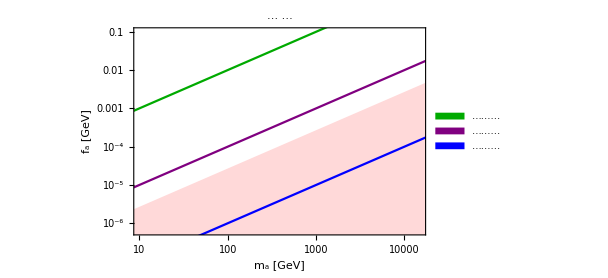

```mathematica
Mirrlim=LogLogPlot[ x/10^6/4,{x,10^-13,10^22},  PlotStyle->LightRed,Filling->Bottom , FillingStyle->LightRed];
Mirr1=LogLogPlot[ x/10^4,{x,10^-13,10^22},PlotStyle->{   Darker[Green]}(*, Filling->Bottom *)];Mirr2=LogLogPlot[  x/10^6,{x,10^-13,10^22},PlotStyle->{    Purple} ];
Mirr3=LogLogPlot[  x/10^8,{x,10^-13,10^22},PlotStyle->{ Blue} ,FrameTicks->{{{ {10^-3,"10^3"}{10^-4,"10^4"},{10^-5,"10^5"},{10^-6,"10^6"},{10^-7,"10^7"} },Automatic},{Automatic,Automatic}},PlotLegends->   { Placed[SwatchLegend[{Darker[Green], Purple,Blue},{"(*GraphicsBox[{Thickness[0.027122321670735017`], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYCYiNjIBBWcTgDBhIOMH7N/R+3jLOlHB64xjvO
mqgE5ztPaBZK40LwhSsnlZzdouig/knl5axOGYcD3fuaTJQlHM5fDXujv1vf
QWHXgn2p58QdbkvXJBqpGjikgUCbuAOv//opqRoGDhogfS/FUPmZCL4J2D1i
Dn++lT6Yo2gAdaeog8y8OM3TF/Qh8p9ZHXYEW0X8V5dzCHjiecn0MjPEfa+l
HP7+B4L6f/YzZgJBpZTDBultuqfefLOHuR/Gh/l/ya3ljw2dGSD+eSnhsN1r
g8WcSgS/RbyWNdONFc4H054ccP5SkP7DvHB+Osi/bgLw8IXxYfbblzjWnr7D
5QBzX7RqhMy5PVDzOGXg/P2gcHWWhfNjQHQNgg/2/3JZiD0+nFB5OQeQsTMj
RR3iQ4LUF6zUcfgPDg85B/c1R5czSMhC9B2Xc+iN6PZnDJCB8yHyuPkw94PN
uy8N579py+02qpbC4MP8LwJKL0ek4eEDNpdDAc4Hm3cewQ/nFGs3nq8I50P8
owzno6dfAJioRx0=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQAmIQrfGWd5/BTEOHl7WPs8/nsDnA+CbGIMAO5xcuL9nw
j5/D4XmW9rfptQh+I8vRfsN0BH9/raxFeoqhQ19Etz9jAbvD8hceev8TDR3S
QGAZmwPY2GBDh36wPJMDt5tqKdMrA4cv+z5uTRdjcCjeKvr7dB2CD7afE8H3
OcFuO3uqvsN/ENjPBHGPrL4DAwgcYHfwBslvNXDY372vyeQxN8T8LkOH+67x
jrM+CsH5YPOuScD5/LEB943SFRyk58VpnhYwcFjx7WXFmQnKkHCYrAPnZ+Z/
aD0pognnp8TecWOWUHNYCeIXKMD5MPNhfLC/Pws4bDH/cSiFS9MhRjVC5lwN
q8N2h6ZHx2fowPmQcNeF8yWmXuHMeKQLEf8MlS/Wg4fn8cNOazP36Tls9dpg
Mafyn73vxYkx/5j1HWbPBALJD/aqT5rnnc0ygPNB1MxMQzgfFr+w+EBPDwDr
HN59
"], CompressedData["
1:eJxTTMoPSmViYGAQA2IQ/R8E+g0cvuz7uDX9moQDjF95/8ct49OiDstfeOj9
LzRwUP+k8nKWp4CD/y3pmsRLeg7bvTZYzKnkctDXWil8IUXPYc5MILjJB+Ef
0XUIfnv544xEQYfnWdrfps/VgfNPHHZamzlPG873vzgx5h+ztkNqGgjww/km
xiDAA+eD3ScGtc9F22EmGHA4JIQEqS/w1HYwAikv5nDYoJe3mNFGy2HJreWP
DZm5HF4XbxX9za3hcJ33tljqNn44H+ZfGD+cU6zduF7RYc4i5Z1/jms53NGU
XfNfWBnijsk6cP52h6ZHxyv04HxYeKWD3a/ogB6eAF/jpCQ=
"], {{15.157800000000002`, 3.15313}, {14.824999999999998`, 2.96875}, {14.512499999999998`, 2.92969}, {14.298399999999999`, 2.92969}, {13.799999999999997`, 2.92969}, {13.721899999999998`, 3.3781300000000005`}, {13.721899999999998`, 3.5250000000000004`}, {13.721899999999998`, 3.80781}, {13.9266, 4.12969}, {14.307799999999999`, 4.12969}, {14.834399999999997`, 4.12969}, {15.049999999999997`, 3.72031}, {15.157800000000002`, 3.15313}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYC4s8bArJnTbdwMDEGgs0iDjD+l30ft6aLicL5
MaoRMudiRB0aWY72G5Yj+A5Nj47PiMbkh7y9/HGGoqiDxlvefQaRFg5RIPk9
Ig43pWsSjVwtHAqWl2z458/nMBMELM0d0kDgGTtEvaYZnC8zL07z9ARTOB9s
/3JjhxKQ/n4uOL/6/o9bxq8l4Hzla4+CGXyUHE4edlqb2WfqsDe/5u3Mr0oO
N4Q+OZ5XM4PzwerNzeF87xPstrNFLRzCOcXajfUVHT6B/O9u4VABMn+1jMMZ
EPCxcFgrpMOXLofg/wcDaYf+4BKV6fkIPiz80Pkw/TB+b0S3P+MHBP/DovUK
ZyWU4fzyw9tcZ+Yi+Cu+vaw4M0HZIVrB8WNyDYIvPvUKZ0YRgs/rv35KagaC
v79W1iI9xMJBpHJSydkQZYj/r5s7gKLf+LGig+qT5nlnq8wd+GMD7htNV3KY
NoG/yuy3GVz/DBCfG8FPib3jxmxhAueDw2+pkUM6KL7KFOD8VgV21TNfJOB8
cHDcF3DYYv7jUIqVCST91LDCzYfxD7UtDz+1yBzOh/kfHN/aAg7o6RcAVcNB
YQ==
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQAWIQzeO/fkoqg4OD+5qjyxl2SDjA+J02nrvShBQcniYu
vGay3s7BGASUlR18L06M+cdsC+f3eL1iMSm0xOCDzetQcrCpjFhhuhbBf56l
/W16rhWcLz71CmdGkZXDim8vK84EIPhnQGCOIpyv/knl5SxPXjh/u9cGizmV
XHDzZDaKzWdawAm3D8aHuQedbwJ2MDvcPzD+lw0B2bOW28H5sPAIfnv544xE
QQf08AIAt+14Fw==
"], CompressedData["
1:eJxTTMoPSmViYGAQA2IQfVXok+N5NnsH9zVHlzPskHCA8Q9272sySRZxqGc5
2m943c6h+v6PW8bcQg42lRErTGvtHILfXv44Q1HAYcoE/iozbzuH1DQgUONz
OAMCe2wdZDaKzWdawOmQv6b7dsYBGzjf/+LEmH+HreH8E4ed1mb6IfgzZgKB
p7UDjyOf1wxNLjj/Pwjs50HjK8L5wpWTSs6mKMHNA/unQwluH4wfLr79IsM+
Gzi/9rdVwbkIWzj/hnRNohGrnYPzhGahNCklB32tlcIXWuwc+GMD7httV4D4
54MdxH55eXh4iYDsPyLtgB6eADlhm+k=
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJhIGYC4s8bArJnhTs6bFB90jwvV9UBxp/S3hp1+Q6U
b+/oEHhLuibRSM3hd0zu0X9KCP7OW11/U/87wPnpaUDwzQGif4+qA8jYs58c
HFg4u+ST+1Qd2peHnzKqcXDYHmwV8Z9dHmJ+uYOD/K4F+1L75OD8GTOBwFLO
IZvz54L0yQ4O913jHWd9lHUQn3qFM2MWgg9SNnMhgg82f4mDQ6sCu+oZETmH
45pWk04vd3CIUY2QORcj5+CqWso0K8DRQW75Cw+9/yoQ9SGODj/fvj5gqYzw
/wa9vMWMNkh8aPgAAPF/hmc=
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3288090890967345],ImageSize->{36.86816438356164, 18.939885429638853`},PlotRange->{{0., 36.87}, {0., 18.939999999999998`}}])","(*GraphicsBox[{Thickness[0.027122321670735017`], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYCYiNjIBBWcTgDBhIOMH7N/R+3jLOlHB64xjvO
mqgE5ztPaBZK40LwhSsnlZzdouig/knl5axOGYcD3fuaTJQlHM5fDXujv1vf
QWHXgn2p58QdbkvXJBqpGjikgUCbuAOv//opqRoGDhogfS/FUPmZCL4J2D1i
Dn++lT6Yo2gAdaeog8y8OM3TF/Qh8p9ZHXYEW0X8V5dzCHjiecn0MjPEfa+l
HP7+B4L6f/YzZgJBpZTDBultuqfefLOHuR/Gh/l/ya3ljw2dGSD+eSnhsN1r
g8WcSgS/RbyWNdONFc4H054ccP5SkP7DvHB+Osi/bgLw8IXxYfbblzjWnr7D
5QBzX7RqhMy5PVDzOGXg/P2gcHWWhfNjQHQNgg/2/3JZiD0+nFB5OQeQsTMj
RR3iQ4LUF6zUcfgPDg85B/c1R5czSMhC9B2Xc+iN6PZnDJCB8yHyuPkw94PN
uy8N579py+02qpbC4MP8LwJKL0ek4eEDNpdDAc4Hm3cewQ/nFGs3nq8I50P8
owzno6dfAJioRx0=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQAmIQrfGWd5/BTEOHl7WPs8/nsDnA+CbGIMAO5xcuL9nw
j5/D4XmW9rfptQh+I8vRfsN0BH9/raxFeoqhQ19Etz9jAbvD8hceev8TDR3S
QGAZmwPY2GBDh36wPJMDt5tqKdMrA4cv+z5uTRdjcCjeKvr7dB2CD7afE8H3
OcFuO3uqvsN/ENjPBHGPrL4DAwgcYHfwBslvNXDY372vyeQxN8T8LkOH+67x
jrM+CsH5YPOuScD5/LEB943SFRyk58VpnhYwcFjx7WXFmQnKkHCYrAPnZ+Z/
aD0pognnp8TecWOWUHNYCeIXKMD5MPNhfLC/Pws4bDH/cSiFS9MhRjVC5lwN
q8N2h6ZHx2fowPmQcNeF8yWmXuHMeKQLEf8MlS/Wg4fn8cNOazP36Tls9dpg
Mafyn73vxYkx/5j1HWbPBALJD/aqT5rnnc0ygPNB1MxMQzgfFr+w+EBPDwDr
HN59
"], CompressedData["
1:eJxTTMoPSmViYGAQA2IQ/R8E+g0cvuz7uDX9moQDjF95/8ct49OiDstfeOj9
LzRwUP+k8nKWp4CD/y3pmsRLeg7bvTZYzKnkctDXWil8IUXPYc5MILjJB+Ef
0XUIfnv544xEQYfnWdrfps/VgfNPHHZamzlPG873vzgx5h+ztkNqGgjww/km
xiDAA+eD3ScGtc9F22EmGHA4JIQEqS/w1HYwAikv5nDYoJe3mNFGy2HJreWP
DZm5HF4XbxX9za3hcJ33tljqNn44H+ZfGD+cU6zduF7RYc4i5Z1/jms53NGU
XfNfWBnijsk6cP52h6ZHxyv04HxYeKWD3a/ogB6eAF/jpCQ=
"], {{15.157800000000002`, 3.15313}, {14.824999999999998`, 2.96875}, {14.512499999999998`, 2.92969}, {14.298399999999999`, 2.92969}, {13.799999999999997`, 2.92969}, {13.721899999999998`, 3.3781300000000005`}, {13.721899999999998`, 3.5250000000000004`}, {13.721899999999998`, 3.80781}, {13.9266, 4.12969}, {14.307799999999999`, 4.12969}, {14.834399999999997`, 4.12969}, {15.049999999999997`, 3.72031}, {15.157800000000002`, 3.15313}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYC4s8bArJnTbdwMDEGgs0iDjD+l30ft6aLicL5
MaoRMudiRB0aWY72G5Yj+A5Nj47PiMbkh7y9/HGGoqiDxlvefQaRFg5RIPk9
Ig43pWsSjVwtHAqWl2z458/nMBMELM0d0kDgGTtEvaYZnC8zL07z9ARTOB9s
/3JjhxKQ/n4uOL/6/o9bxq8l4Hzla4+CGXyUHE4edlqb2WfqsDe/5u3Mr0oO
N4Q+OZ5XM4PzwerNzeF87xPstrNFLRzCOcXajfUVHT6B/O9u4VABMn+1jMMZ
EPCxcFgrpMOXLofg/wcDaYf+4BKV6fkIPiz80Pkw/TB+b0S3P+MHBP/DovUK
ZyWU4fzyw9tcZ+Yi+Cu+vaw4M0HZIVrB8WNyDYIvPvUKZ0YRgs/rv35KagaC
v79W1iI9xMJBpHJSydkQZYj/r5s7gKLf+LGig+qT5nlnq8wd+GMD7htNV3KY
NoG/yuy3GVz/DBCfG8FPib3jxmxhAueDw2+pkUM6KL7KFOD8VgV21TNfJOB8
cHDcF3DYYv7jUIqVCST91LDCzYfxD7UtDz+1yBzOh/kfHN/aAg7o6RcAVcNB
YQ==
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQAWIQzeO/fkoqg4OD+5qjyxl2SDjA+J02nrvShBQcniYu
vGay3s7BGASUlR18L06M+cdsC+f3eL1iMSm0xOCDzetQcrCpjFhhuhbBf56l
/W16rhWcLz71CmdGkZXDim8vK84EIPhnQGCOIpyv/knl5SxPXjh/u9cGizmV
XHDzZDaKzWdawAm3D8aHuQedbwJ2MDvcPzD+lw0B2bOW28H5sPAIfnv544xE
QQf08AIAt+14Fw==
"], CompressedData["
1:eJxTTMoPSmViYGAQA2IQfVXok+N5NnsH9zVHlzPskHCA8Q9272sySRZxqGc5
2m943c6h+v6PW8bcQg42lRErTGvtHILfXv44Q1HAYcoE/iozbzuH1DQgUONz
OAMCe2wdZDaKzWdawOmQv6b7dsYBGzjf/+LEmH+HreH8E4ed1mb6IfgzZgKB
p7UDjyOf1wxNLjj/Pwjs50HjK8L5wpWTSs6mKMHNA/unQwluH4wfLr79IsM+
Gzi/9rdVwbkIWzj/hnRNohGrnYPzhGahNCklB32tlcIXWuwc+GMD7httV4D4
54MdxH55eXh4iYDsPyLtgB6eADlhm+k=
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJhIGYC4s8bArJnhTs6bFB90jwvV9UBxp/S3hp1+Q6U
b+/oEHhLuibRSM3hd0zu0X9KCP7OW11/U/87wPnpaUDwzQGif4+qA8jYs58c
HFg4u+ST+1Qd2peHnzKqcXDYHmwV8Z9dHmJ+uYOD/K4F+1L75OD8GTOBwFLO
IZvz54L0yQ4O913jHWd9lHUQn3qFM2MWgg9SNnMhgg82f4mDQ6sCu+oZETmH
45pWk04vd3CIUY2QORcj5+CqWso0K8DRQW75Cw+9/yoQ9SGODj/fvj5gqYzw
/wa9vMWMNkh8aPgAAPF/hmc=
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3288090890967345],ImageSize->{36.86816438356164, 18.939885429638853`},PlotRange->{{0., 36.87}, {0., 18.939999999999998`}}])","(*GraphicsBox[{Thickness[0.027122321670735017`], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYCYiNjIBBWcTgDBhIOMH7N/R+3jLOlHB64xjvO
mqgE5ztPaBZK40LwhSsnlZzdouig/knl5axOGYcD3fuaTJQlHM5fDXujv1vf
QWHXgn2p58QdbkvXJBqpGjikgUCbuAOv//opqRoGDhogfS/FUPmZCL4J2D1i
Dn++lT6Yo2gAdaeog8y8OM3TF/Qh8p9ZHXYEW0X8V5dzCHjiecn0MjPEfa+l
HP7+B4L6f/YzZgJBpZTDBultuqfefLOHuR/Gh/l/ya3ljw2dGSD+eSnhsN1r
g8WcSgS/RbyWNdONFc4H054ccP5SkP7DvHB+Osi/bgLw8IXxYfbblzjWnr7D
5QBzX7RqhMy5PVDzOGXg/P2gcHWWhfNjQHQNgg/2/3JZiD0+nFB5OQeQsTMj
RR3iQ4LUF6zUcfgPDg85B/c1R5czSMhC9B2Xc+iN6PZnDJCB8yHyuPkw94PN
uy8N579py+02qpbC4MP8LwJKL0ek4eEDNpdDAc4Hm3cewQ/nFGs3nq8I50P8
owzno6dfAJioRx0=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQAmIQrfGWd5/BTEOHl7WPs8/nsDnA+CbGIMAO5xcuL9nw
j5/D4XmW9rfptQh+I8vRfsN0BH9/raxFeoqhQ19Etz9jAbvD8hceev8TDR3S
QGAZmwPY2GBDh36wPJMDt5tqKdMrA4cv+z5uTRdjcCjeKvr7dB2CD7afE8H3
OcFuO3uqvsN/ENjPBHGPrL4DAwgcYHfwBslvNXDY372vyeQxN8T8LkOH+67x
jrM+CsH5YPOuScD5/LEB943SFRyk58VpnhYwcFjx7WXFmQnKkHCYrAPnZ+Z/
aD0pognnp8TecWOWUHNYCeIXKMD5MPNhfLC/Pws4bDH/cSiFS9MhRjVC5lwN
q8N2h6ZHx2fowPmQcNeF8yWmXuHMeKQLEf8MlS/Wg4fn8cNOazP36Tls9dpg
Mafyn73vxYkx/5j1HWbPBALJD/aqT5rnnc0ygPNB1MxMQzgfFr+w+EBPDwDr
HN59
"], CompressedData["
1:eJxTTMoPSmViYGAQA2IQ/R8E+g0cvuz7uDX9moQDjF95/8ct49OiDstfeOj9
LzRwUP+k8nKWp4CD/y3pmsRLeg7bvTZYzKnkctDXWil8IUXPYc5MILjJB+Ef
0XUIfnv544xEQYfnWdrfps/VgfNPHHZamzlPG873vzgx5h+ztkNqGgjww/km
xiDAA+eD3ScGtc9F22EmGHA4JIQEqS/w1HYwAikv5nDYoJe3mNFGy2HJreWP
DZm5HF4XbxX9za3hcJ33tljqNn44H+ZfGD+cU6zduF7RYc4i5Z1/jms53NGU
XfNfWBnijsk6cP52h6ZHxyv04HxYeKWD3a/ogB6eAF/jpCQ=
"], {{15.157800000000002`, 3.15313}, {14.824999999999998`, 2.96875}, {14.512499999999998`, 2.92969}, {14.298399999999999`, 2.92969}, {13.799999999999997`, 2.92969}, {13.721899999999998`, 3.3781300000000005`}, {13.721899999999998`, 3.5250000000000004`}, {13.721899999999998`, 3.80781}, {13.9266, 4.12969}, {14.307799999999999`, 4.12969}, {14.834399999999997`, 4.12969}, {15.049999999999997`, 3.72031}, {15.157800000000002`, 3.15313}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYC4s8bArJnTbdwMDEGgs0iDjD+l30ft6aLicL5
MaoRMudiRB0aWY72G5Yj+A5Nj47PiMbkh7y9/HGGoqiDxlvefQaRFg5RIPk9
Ig43pWsSjVwtHAqWl2z458/nMBMELM0d0kDgGTtEvaYZnC8zL07z9ARTOB9s
/3JjhxKQ/n4uOL/6/o9bxq8l4Hzla4+CGXyUHE4edlqb2WfqsDe/5u3Mr0oO
N4Q+OZ5XM4PzwerNzeF87xPstrNFLRzCOcXajfUVHT6B/O9u4VABMn+1jMMZ
EPCxcFgrpMOXLofg/wcDaYf+4BKV6fkIPiz80Pkw/TB+b0S3P+MHBP/DovUK
ZyWU4fzyw9tcZ+Yi+Cu+vaw4M0HZIVrB8WNyDYIvPvUKZ0YRgs/rv35KagaC
v79W1iI9xMJBpHJSydkQZYj/r5s7gKLf+LGig+qT5nlnq8wd+GMD7htNV3KY
NoG/yuy3GVz/DBCfG8FPib3jxmxhAueDw2+pkUM6KL7KFOD8VgV21TNfJOB8
cHDcF3DYYv7jUIqVCST91LDCzYfxD7UtDz+1yBzOh/kfHN/aAg7o6RcAVcNB
YQ==
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQAWIQzeO/fkoqg4OD+5qjyxl2SDjA+J02nrvShBQcniYu
vGay3s7BGASUlR18L06M+cdsC+f3eL1iMSm0xOCDzetQcrCpjFhhuhbBf56l
/W16rhWcLz71CmdGkZXDim8vK84EIPhnQGCOIpyv/knl5SxPXjh/u9cGizmV
XHDzZDaKzWdawAm3D8aHuQedbwJ2MDvcPzD+lw0B2bOW28H5sPAIfnv544xE
QQf08AIAt+14Fw==
"], CompressedData["
1:eJxTTMoPSmViYGAQA2IQfVXok+N5NnsH9zVHlzPskHCA8Q9272sySRZxqGc5
2m943c6h+v6PW8bcQg42lRErTGvtHILfXv44Q1HAYcoE/iozbzuH1DQgUONz
OAMCe2wdZDaKzWdawOmQv6b7dsYBGzjf/+LEmH+HreH8E4ed1mb6IfgzZgKB
p7UDjyOf1wxNLjj/Pwjs50HjK8L5wpWTSs6mKMHNA/unQwluH4wfLr79IsM+
Gzi/9rdVwbkIWzj/hnRNohGrnYPzhGahNCklB32tlcIXWuwc+GMD7httV4D4
54MdxH55eXh4iYDsPyLtgB6eADlhm+k=
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJhIGYC4s8bArJnhTs6bFB90jwvV9UBxp/S3hp1+Q6U
b+/oEHhLuibRSM3hd0zu0X9KCP7OW11/U/87wPnpaUDwzQGif4+qA8jYs58c
HFg4u+ST+1Qd2peHnzKqcXDYHmwV8Z9dHmJ+uYOD/K4F+1L75OD8GTOBwFLO
IZvz54L0yQ4O913jHWd9lHUQn3qFM2MWgg9SNnMhgg82f4mDQ6sCu+oZETmH
45pWk04vd3CIUY2QORcj5+CqWso0K8DRQW75Cw+9/yoQ9SGODj/fvj5gqYzw
/wa9vMWMNkh8aPgAAPF/hmc=
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3288090890967345],ImageSize->{36.86816438356164, 18.939885429638853`},PlotRange->{{0., 36.87}, {0., 18.939999999999998`}}])"}, LegendMarkers ->"Bubble",LegendMarkerSize->10,LabelStyle->{FontSize->5}],{0.85,.16
}] }];
Show[qcdAxion,Mirrlim,(*xdAxionlimit,*)(*LabDataplotDNew, AstroLimitsplotDNew,*)qcdAxion,Mirr1,Mirr2,Mirr3, Frame->True,FrameStyle->Directive[Black,12,Thickness[0.0021]],ImageSize->450,Axes->False]
```

## Grand Color Model

```mathematica
MaTeX[Grand  , FontSize->18 ]
```

-Graphics-

```mathematica
MaTeX[ Color, FontSize->18 ]
```

-Graphics-

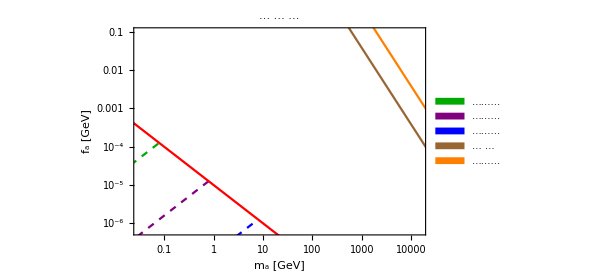

```mathematica
qcdAxion=LogLogPlot[ x/0.005625 ,{x,10^-14,10^10},PlotStyle->Black  ,PlotRange->{{10^-1.5,1.5*10^4},{10^-6.2,10^-1}},Frame-> True, FrameTicks->ticksList,FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]}, PlotLabel->"(*GraphicsBox[{Thickness[0.020868113522537562`], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIbIGYCYvEer1csU7QcXhVvFf29Wt0Bxq/+tCEge5aG
Q0rsHTfmHZoOsxcp7/zTruFQ99uq4NwJdThfal6c5ukLanC++5qjyxlWKML1
w/gw8yvv/7hlvFsJzj+xa0cv2wVVOF9i6hXOjEeqDh77a2Ut3BH8Ke2tUZf/
qML54Zxi7cbzleH8GNUImXMx8g7OE5qF0qwUIfbukHMoPbzNdaasApw/ayYQ
3JSA86NB+mo4HfhjA+4bPVeE8x9EiG+/6KAN5z/P0v423dfI4WD3viaTxRIO
Jw87rc3sM3b4su/j1vRp8nC+B8jcG8pw/hxQuBxXc7CtjFhhetbQQVdR/ktO
mbqDzPIXHnrz9RxqQeHZAeSDwtEAwT8B0i+n53Dhatgb/dsI/n8QsNfA4MP0
w/hge64h+NxuqqVMq4zh/BgFx4/Jf4wdGliO9huaaziAot2E0QQi/18dzofZ
D+P//Vb6YM5Fdbh+MH+iuoP3CXbb2UeNHU6B3PVP1QEUfekuRpB4s1GBuC/B
2CE9DQjElBy8QOpZTRx2BFtF/F8uh8pPF4LzX9Q+zj6v89e+G2R/oCGcD4sf
GP/DovUKZ18oO/RHdPszGgg5vGnL7Ta6LeNwBgzk4PxyUHrwVYLzwelHSdVB
dteCfanv5CDut1Nz6Lbx3JXWpOhQA0rHt9QcQMlmJqcCPDzuu8Y7zhKUg8QX
hwacDwtPGB8W3iKVk0rOqiD4YPvy5OF8U5u9QdMU1eD8F6D0VqvucB5kX7QG
Rv6E8QGz7bal
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYC4kaWo/2G340dMvI/tJ68ouMA49d82hCQ/UvX
4UCtrEV6irHDn2+lD+Zs1HPg918/JfWEEZy/QS9vMWOOIZyvr7VS+MIVA4ct
5j8OpXDpOFwX+uR4fpmBQ0JIkPqCk1oOy1946P1fiMlHMU9G1+EMCPgg+CcO
O63NjNN1mDETCCz14fwXxVtFf3frO7jvBzpUHcF/krjwmkm+Npz/ftF6hbMV
inC+8rVHwQwyChB96foOEaoRMufuyMPtQ+f/BwNZh+0OTY+O/9B1EKmcVHJW
RQ7ijnn6cH56GhC4GcD5IOUzTiP4t6VrEo22GsL5PV6vWEwMjeDmw/gw+8Hh
98wAzgcrW4/Jr77/45ZxtyKcnwmKzxJ1OL+FFxhxT7Xg8QV2t5yeg//FiTH/
Dhuh8h+j8ZmNHXxOsNvOFtVzAAeXCiJ9oPPB4b7fCBJPOxH8qRP4q8xO68D5
YPq9NiS8xIwdTIyBYLK2w3SQumgEX2LqFc6MSQg+LH2KgALqCoIPS78AqE1I
jQ==
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}}}, {CompressedData["
1:eJxTTMoPSmViYGCwBGIQ/edb6YM5hTYODCBgoOQA4/8F0YYqDk8SF14zkcfk
88cG3DdSV4LzeyO6/Rk/yDuYGAPBYmuHGNUImXMx8g5fNgRkz0pH8O2bHh2f
sdoKg199/8ct425FOD+cU6zdWF4Zzp+zSHnnH3cNOF9fa6XwhSVacH56GhA8
03ZQf9I87+wrS4c3xVtFf3vrOnR7vWIxcbR0qPkEdEiVnsNGvbzFjDUWDrqK
8l9yrulB/P3AHM7/svNW199SMzi/cE337YwCU4fnWdrfps/VgfP/g4C9Fpx/
+gwQvNFw4HJTLWX6ZepQDbLvloaDzwl229miZnB+D8g9gQi+Ksi9u8wc/C5O
jPmnrAnng/2nogXnJ4QEqS/g1HZYcn8f35xkM0i452vDzYfxweHPjODHKDh+
TH5j6tDC679+Sqq2w6nDTmsz75k6TGlvjboco+1QAgym03ZmDidA4vN0HUDB
mGZm7vDj7esDls56DjeEPjmev4bgR4PM22MB5/OAjN1h6XB8145etg06cP56
kMPXasL5M0FAEho+qywcPPbXylqwazgcAFLpKeYQd+1Th/tvxgT+KrPVag4S
U69wZjiZQvyfqQqJrw8mkPQxXxnO77bx3JXmpATnh7y9/HEGo7wDKFrO9JhB
6BxZiHyDOZwPSw8w/ldQ/KdaOqSAwmGZvIMKKPxPWTqUHt7mOvOuooMPKJ4u
Wzo4T2gWSvNScAB5Iz3EyuHLvo9b07fJQsJRzhrOPw7i1yH4sPzlvubocoYd
cg7o+Q8A0h+N6A==
"], {{25.720299999999995`, 9.990630000000001}, {25.720299999999995`, 8.431249999999999}, {24.609399999999997`, 7.643750000000001}, {23.625, 7.643750000000001}, {22.729699999999998`, 7.643750000000001}, {22.0297, 8.306249999999999}, {22.0297, 9.129690000000002}, {22.0297, 9.667189999999998}, {22.262500000000003`, 10.617199999999997`}, {23.301599999999997`, 11.1906}, {24.162499999999998`, 11.6734}, {25.1469, 11.7453}, {25.720299999999995`, 11.781300000000002`}, {25.720299999999995`, 9.990630000000001}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGITIGYCYh7/9VNSFzg5/AcDWQcYP0I1QubcHXkH7xPs
trN5Efz9tbIW6SxODsYgIKwA579ftF7hbIUinO9/cWLMv8eacH5K7B035h3a
EPPeOjr8+Vb6YM5GPYfV3bczGO47wPkX8+PZz2ki+B82BGTPmm7vYGqzN2ha
o47Dgbbl4aeC7B1MwPZrO0SIb7/I4IfJh+mXmBenedrA1uEMCPgg+CcOO63N
jNN16A0uUZlubwfn1/62KjiXYefgDnK4OoL/JHHhNZN8bTgf5l8YX/nao2AG
GQWH1DQgCLODhxfMPnQ+LLzB5s63dRCpnFRyVkUObh6MD1Z2H8GvZznabxhu
D+erPmmed1bIAc4Hh5+nA9x8GB9mP9ifefZw/ga9vMWMMfbw+ITxYf6D8WeC
QKQGnN/CC0woS7Ud0kH+1XOAmCun51C8VfT36XMIvqtqKdOsCkc4Xx3k3i5H
B3NQfB7UhvPrQf7m0ILzYfbD+LDwvQzyT6Mj3P1rQOnnvQMGH+Z/cHpQc4SH
D8w8GH++jc6VWccQ/Pv7+OYYMznB+QmHL2unZiL46PkFAHPkZ1c=
"]], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}}}, {CompressedData["
1:eJxTTMoPSmViYGCQAmIQXffbquCcgbvDfzCQdYDxI1QjZM7dkXdIOHxZO3Wl
G5x/BgSmuDnsza95O1NVAc4vPbzNdeZdRTi/ZKvo79PvjB026uUtZmxxdYhR
cPyYvAfBvyldk2jkauxgYgwE3G5wPgMIKLg5zAQBTQT/eZb2t+m+RnD+Voem
R8ctdCD2iLk5pKaBgI5DLcj9O1wd/nwrfTBno57Dmu7bGQz/XeB81sWTrBhF
EfzlLzz0/hs6OzxJXHjNJF8bzhft8XrFskUNzu+28dyVxqTksPNW199UdheI
P3NkIe55geD/ick9+m+VK5x/QtNq0ml+N4c7mrJr/gsrOuRw/lyQLg3lByP4
MPXo8QEAOuy9Pw==
"], CompressedData["
1:eJxTTMoPSmViYGAQAWIQncP5c0G6tJvDGRDwUXaA8WfMBAJLJYdlLzz0/n90
dXjgGu84y1HRQeiT4/m0va4OzhOahdK6FBx23ur6m5rv6iC7a8G+1HdyDomH
L2unKro6mBgDwWQ5BwXHj8lnvrrA+WDzNyP4YHuPODukpAHBMnk4f8YE/iqz
1Wpwvsy8OM3TG3QdSraK/j59zsXhxGGntZlyeg4SU69wZnC5wvkb9fIWM5Yg
+HW/rQrOnXB1OL5rRy+bga6Dzwl229l/XR3SQfY904b7t4XXf/0UVQQ/ISRI
fQEngq+vtVL4QoqWA3p4AQBmOYss
"]}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3169518292168768],ImageSize->{47.914590286425906`, 23.511820672478205`},PlotRange->{{0., 47.92}, {0., 23.51}}]) (*GraphicsBox[{Thickness[0.02424830261881668], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYC4v8gYK/hIDH1CmdGkroDjH/qsNPazH0IPlj+
kbrDBtUnzfPeqsP5fhcnxvxbjMn32F8ra3Fc3eHC1bA3+rPVHTLzP7SeLFF3
+Put9MGcQHWHld9eVpwpUHJQufYomGGPsoP7mqPLGXbIObxpy+022i0P5589
AwQ5EnB+tGqEzLkaToi73ivC+Q8ixLdfdNCG859naX+b7mvkcLB7X5PJYgmH
kyD/9Bk7fNn3cWv6NHk43wNk7g1lOH/OIuWdf46rOdhWRqwwPWvooKso/yWn
TN1BZvkLD735eg61v60KznUA+fPiNE8bIPgnQPrl9CD+vY3gw8IPnQ/TD+OD
7bmG4HO7qZYyrTKG82MUHD8m/zF2aGA52m9oruHQ4/WKxYTRBCL/Xx3Oh9kP
44PD+6I6XD+YP1HdwfsEu+3so8aQeP6n6gCKrnQXI4cp7a1Rl21UIO5LMHZI
TwMCMSUHL5B6VhOHHcFWEf+Xy6Hy04Xg/Be1j7PP6/y17wbZH2gI58PiB8Y/
AwbKcP3geL8tA41/OTh/h0PTo+M3VOB8WHiYGAOBszJq+gSmXwBN+FiR
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{20.721899999999994`, 11.334400000000002`}, {20.721899999999994`, 13.626599999999996`}, {19.054699999999997`, 15.4188}, {17.103099999999998`, 15.4188}, {15.149999999999999`, 15.4188}, {13.4844, 13.626599999999996`}, {13.4844, 11.334400000000002`}, {13.4844, 9.076559999999999}, {15.149999999999999`, 7.356249999999999}, {17.103099999999998`, 7.356249999999999}, {19.054699999999997`, 7.356249999999999}, {20.721899999999994`, 9.076559999999999}, {20.721899999999994`, 11.334400000000002`}}, CompressedData["
1:eJxTTMoPSmViYGCQBGIQbWIMBJONHUR7vF6xfFFzgPFZOLvkk/tUHXjcVEuZ
uowdPNYcXc6QoewQIb79IgOfsQMDCGxQdHiepf1teq+Rw0wQ4FRw4PdfPyX1
hKGDO0j9DjmHLeY/DqVIIfgH25aHn3IygPN1FeW/5IjpO5wBgRgFhx9vXx+w
dNZz6Lbx3JV2SNHhxGGntZlxug7hnGLtxvHKDuJTr3BmOOk6PAI5JEEVzoe5
H8b3PsFuO7tUwyEj/0PryRBdB/9b0jWJQVpw858kLrxm8l7b4fzVsDf6v/Ug
/pDVdShc0307w8AArg7mfhi//rdVwbkXCP51oU+O56cZwd1poLVS+AKLscOU
9taoyzI68PBcr/qkeV6uFpwvNS9O87SAhgN6+AMAf4qjMw==
"]}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIxIGYC4rrfVgXnNCwd/oOBrAOMH6EaIXPujryDMQgw
W8D5MvPiNE9/MIeICyvA+e8XrVc4W6EI55dsFf19+p2xw5PEhddMzps6xCg4
fkzeg+DflK5JNHI1dniRpf1t+l0zOP+G0CfH82zmDjNBQBPBfw5S52sE58Ps
g/GVrz0KZpBRcDDQWil84YsZ3L0w+9D5MP/aVUasMLU1cxCpnFRyVkUObh6M
D3ZHJYIP8x+Mr/qked7ZXRZwPnp4AgDzB538
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{33.421899999999994`, 11.334400000000002`}, {33.421899999999994`, 13.626599999999996`}, {31.7547, 15.4188}, {29.80309999999999, 15.4188}, {27.849999999999994`, 15.4188}, {26.184400000000007`, 13.626599999999996`}, {26.184400000000007`, 11.334400000000002`}, {26.184400000000007`, 9.076559999999999}, {27.849999999999994`, 7.356249999999999}, {29.80309999999999, 7.356249999999999}, {31.7547, 7.356249999999999}, {33.421899999999994`, 9.076559999999999}, {33.421899999999994`, 11.334400000000002`}}, CompressedData["
1:eJxTTMoPSmViYGCQBGIQbQwCyg4Ooj1er1i+qDnA+CycXfLJfaoO8210rsyS
c3DwWHN0OUOGsgNImclBewcGENig6CAxL07ztIO9w0wQ4FRwsG96dHxGtZ2D
O0j9DjmHp1na36aftYXzv+681fX3qw2cf/yw09pMOxuHMyAQo+Cgr7VS+MIV
a4duG89daYeA5k+9wpmRZO0QzinWbhyv7LC/VtYiPcTa4VGE+PaLCapwPsz9
ML73CXbb2aUaDs9B9sdaO/jfkq5JDNKCm/8kceE1k/faEPcb2EDUyeo6LLm/
j2/OYxuHH29fH7B01oO7H8bfoJe3mHGOHZzP4aZayuRl73AC5I84XYeU2Dtu
zDvsHaa0t0ZdltGBh+d61SfN83K14HwpkL0CGg7o4Q8AiuSgbg==
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJdIGYC4pKtor9Pv3N2yMj/0Hryio4DjF/zaUNA9i9d
B+FPjufTljo7/PlW+mDORj2Hnbe6/qaGI/jdXq9YTFY6wfneJ9htZ8c6OWwx
/3EohUvHYb6NzpVZbk4OCSFB6gtOajm0Lw8/ZeSCyYfpv7+Pb46xlaPDGRDw
QfBPHHZamxmn6zATBA4i+LoTFvwwvObo4L6/VtZCHcF/krjwmkm+Npz/ftF6
hbMVinC+8rVHwQwyCg4siydZMZ51dIhQjZA5d0cebh86/z8YyDokHr6snVro
6CBSOankrIqcg+qT5nlnbyH46WlAIOYE5weXqEz/H4Hgyzt+TD5zFsGviFhh
epbbGW4+jA+zHxx+aU5wvjEIeGPyq+//uGXcrQjnZ4Lis0Qdzm/h9V8/5akW
PL7A4Sen53BbuibRKNQZzr8J4qc6o8qXOjv4gOJVVA+SHlrR0gcSHxweQc4O
M0DxtBPBnzqBv8rstA6cD46f99qQ8KpzdjABuXOytkP9b6uCcwsQ/APAaE3f
g+DD0qdID9AjVxB8WPoFAMbPPHY=
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3169518292168768],ImageSize->{41.240627646326274`, 23.511820672478205`},PlotRange->{{0., 41.24}, {0., 23.51}}]) (*GraphicsBox[{Thickness[0.021344717182497336`], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJbIGYC4hZe//VTWvUc/oOBrAOMH6EaIXPujrzDi+Kt
or+5deB89/21shbLtTH41fd/3DLuVoTzrwt9cjxfZgTn35SuSTRyNYabB+PD
7EPnxyg4fkzeY+yQEnvHjfmHJpyfDOJbIPjMnF3yyXqaDp83BGTP2m7s0MBy
tN/wu4bD4bbl4aeKjB2cJzQLpVkpOvDHBtw3eq7oMBMEfgrB5SvB7haC6wfL
VwrBzXdfc3Q5ww8BON/EGAT+26PzYe6PBoVLDSfcPyXLSzb84+fG4MPCB8YH
G9OsBOeXHt7mOnOuIpwPC2+Yfeh8WPwd7N7XZPKYyUGkclLJWRU5B25HPq8Z
LzngfAYQaOCB89U/qbycxSkA5589AwQ8wnD+A9d4x1kbReDpA8aHp4/ax9nn
3/Bi8GHuh/Fh/oPxweFvZOzg/8TzkqkwH5wPtua+PNR+eQdhEC2i4CC7a8G+
1Dw5SDyqK8Dds/Lby4ozBQj+DFD87UTwla89CmY4g9APVv9BAW4+Eyj95GlC
4t0Tmr4qMPmw9A3jw/xrBPKXMIJf8wmUkNQw+DD3/P1W+mDORHV4+D6KEN9+
sUETzp8ygb/KrFsLzs/I/9B6coo2nL9W9UnzvF5dOB89/wIAaZSptA==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{23.921899999999994`, 11.334400000000002`}, {23.921899999999994`, 13.626599999999996`}, {22.2547, 15.4188}, {20.3031, 15.4188}, {18.349999999999998`, 15.4188}, {16.684399999999997`, 13.626599999999996`}, {16.684399999999997`, 11.334400000000002`}, {16.684399999999997`, 9.076559999999999}, {18.349999999999998`, 7.356249999999999}, {20.3031, 7.356249999999999}, {22.2547, 7.356249999999999}, {23.921899999999994`, 9.076559999999999}, {23.921899999999994`, 11.334400000000002`}}, CompressedData["
1:eJxTTMoPSmViYGCQBGIQnQYCx8wcRHu8XrF8UXOA8Vk4u+ST+1Qd7CojVpju
NXPwWHN0OUOGsgNImYmjmQMDCGxQdJCZF6d5+oCpw0wQ4FRwcGx6dHzGbxMH
d5D6HXIOL7K0v033RfC/7LzV9bfUGM4/fdhpbeY+I4czIBCj4KCvtVL4QoiR
Q7eN5660Q4oO4lOvcGY8MnQI5xRrN45XdthfK2uRfsXQ4VGE+PaLCapwPsz9
ML73CXbb2aUaDs9B9t81dPC/JV2TGKQFN/9J4sJrJu+1HaRB7t9gBFEnq+uw
5P4+vjnJxg4/3r4+YOmsB3c/jL9RL28xo4wpnM/jplrKdMrU4QTIH3G6Dimx
d9yYLcwcprS3Rl2W0YGH53rVJ83zcrXgfCmQvQIaDujhDwBVS6hT
"]}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}}}, {CompressedData["
1:eJxTTMoPSmViYGCQAmIQ7X2C3Xb2XgeH/2Ag6wDjR6hGyJy7I++gO2HBD0Mz
BH8mCCg6OOzNr3k7U1UBzi89vM115l1FOL9kq+jv0++MHf58K30wR9HOIUbB
8WPyHgT/pnRNopGrMcRefXs4fwZIf6Q9xBxNBP95lva36b5GcP5Wh6ZHxy10
HOpZjvYbuts7pKaBgI7DlAn8VWbddhB7Nuo5fNgQkD1L3BbOX3J/H98cZ2s4
H2xuraXDk8SF10zyteF80R6vVyxb1OD8bhvPXWlMSg48/uunpGpYO5wBgRxZ
iHte2sD5/cElKtPz7eB89be8+wws7R3uaMqu+S+s6FCwpvt2RgCUH4zgw9Sj
xwcATSbIVg==
"], CompressedData["
1:eJxTTMoPSmViYGAQAWIQXbCm+3ZGgL3DGRDwUXaA8WfMBAJLJYenWdrfpv+1
c3jgGu84y1HRYW+trEX6FDsH5wnNQmldCg48/uunpP6wdZDdtWBf6js5hxgF
x4/JMbYOJsZAMFnO4YZ0TaIRK4KfDzK/wQbOB9OLrRxS0oBgmTycP2MCf5XZ
ajU4X2ZenObpDboODSxH+w232zicOOy0NlNOD0Lr2cL5f76VPpjDaAfnTwWb
Y+dwfNeOXjYDXQd9rZXCF0TsHdJB9j3Thvu3hRfoEVUEPyEkSH0BJ4IP1pei
5YAeXgC79oGj
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQAGIQ/WlDQPaseheHU4ed1mb+U3eA8Vt4/ddPWartUBGx
wvQss4uDrqL8l5xreg7paUDwzwnOz+b8uSCdG8FXf9I876yXo0NK7B03Zgtt
OP9p4sJrJufV4Hz+2ID7RupKDlO+scXPUHFyOAMCObIOn0H2izvD+TxAZ6RK
uMD5Qp8cz6fVujgYg0CzEpxvAuI7K8P5dzRl1/xvVnb4E5N79F8WAX4Ugu+q
Wso0K8LF4YFrvOOsQmWHnbe6/qb6Q+1jVnZgWTzJilEWyp+s4LCm+3YGw3xn
B/c1R5cz7JCDuF8dwQerP+oE54tPvcKZkQTlWyjA/V99/8ct49OKDsIg9991
dAjnFGs3nq8M509pb426vEcVzp8xgb/KLFvdARQdaWUucD4s/k7s2tHLNgHB
lwDZuwjBh8U3AMCs3Do=
"], {{40.02969999999999, 11.9781}, {35.7484, 11.9781}, {35.8734, 14.557799999999999`}, {37.25309999999999, 15.131299999999996`}, {37.9703, 15.131299999999996`}, {39.1875, 15.131299999999996`}, {40.012499999999996`, 13.9844}, {40.02969999999999, 11.9781}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIxIGYC4gjx7RcZ1rk5/AcDWQcYP0I1QubcHXkHE2Mg
kEbwl73w0Psv6OYAEjYWVoDz3y9ar3C2QhHOL9kq+vv0O2OHHq9XLCaMrg4x
Co4fk/cg+DelaxKNXI0deP3XT0ntQPBZFk+yYpzr6jATBDQR/OdZ2t+m+xrB
+TD7YHzla4+CGWQUHDbq5S1mnOIKdy/MPnQ+zL8W147mmli4OohUTio5qyIH
Nw/GTwOBawg+zH8w/pru2xkM5Qg+engCAOIukE0=
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.3169518292168768],ImageSize->{46.853858032378575`, 23.511820672478205`},PlotRange->{{0., 46.849999999999994`}, {0., 23.51}}])"];

GCm1=LogLogPlot[ 4*Pi*3000/x^2,{x,10^-13,10^22},PlotStyle->{ Brown} ];GCm2=LogLogPlot[  4*Pi*30000/x^2,{x,10^-13,10^22},PlotStyle->{Orange} ];
GC1=LogLogPlot[ (4*Pi)^2*x/(10^(-5)*L^2)/.{L-> 10^5},{x,10^-13,10^22},PlotStyle->{Dashed,  Darker[Green]}(*, Filling->Bottom *)];GC2=LogLogPlot[  (4*Pi)^2*x/(10^(-5)*L^2)/.{L-> 10^6},{x,10^-13,10^22},PlotStyle->{Dashed,   Purple} ];
GC3=LogLogPlot[  (4*Pi)^2*x/(10^(-5)*L^2)/.{L-> 10^7},{x,10^-13,10^22},PlotStyle->{Dashed,Blue} ,PlotLegends->   { Placed[SwatchLegend[{Darker[Green],Purple, Blue},{"","","" }, LegendMarkers ->"Bubble",LegendMarkerSize->10,LabelStyle->{FontSize->5}],{0.18,.8}] ,Placed[SwatchLegend[{Brown,Orange},{"  ","" }, LegendMarkers ->"Bubble",LegendMarkerSize->10,LabelStyle->{FontSize->5}],{0.86,.25}] }];

GC0=LogLogPlot[  10^(-5)/x,{x,10^-13,10^22},PlotStyle->{Red},Filling->Top,FillingStyle->White];
Show[qcdAxion,GC2,GC3,GC1,GC0,GCm1,GCm2, Frame->True,FrameStyle->Directive[Black,12,Thickness[0.0021]],ImageSize->450,Axes->False]
```

```mathematica
MaTeX[Subscript[m, V]]
```

-Graphics-

```mathematica
MaTeX["=", FontSize->14]
```

-Graphics-

```mathematica
-Graphics--Graphics-
```

```mathematica
MaTeX[30, FontSize->14]
```

-Graphics-

```mathematica
MaTeX[3, FontSize->14]
```

-Graphics-

```mathematica
MaTeX[TeV, FontSize->14]
```

-Graphics-

```mathematica
MaTeX["="10^("7"), FontSize->14]
```

-Graphics-

```mathematica
MaTeX[Subscript[Λ, Sp], FontSize->14]
```

-Graphics-

```mathematica
MaTeX[Subscript[m, V], FontSize->14]
```

-Graphics-